# GPT Bell Experiment

Author : Patrick Daley
Lab Group: Kevin Resch’s QOQI at University of Waterloo
Version: 8
Mathematica Version: 11.1.1.0
Date of Fork with version 2: August 28 2018

Summary: This notebook is used for generalized probabilistic theory (GPT) tomography of a Bell state in the polarization degree of freedom. It outputs the needed waveplate (WP) angles for the measurements as well as reconstructs the density matrix using standard quantum state tomography (QST). The code also has a section to simulate the experiment in order to generate data to test the data analysis (done in MATLAB). Developed with the support of the Institute for Quantum Computing (IQC), NSERC and the University of Waterloo.

Version 2 adds the ability to do signalling and the simulation code is properly written.

Version 3 incorporates the changes discussed in the meeting with Rob at Perimeter in August 2018. The signalling will be done in post (so it’s direct and cannot be regrouped) and the fitting will be able to be constrained to a specific GPT theory, classical and quantum in particular.

Version 4 does the causal fitting by doing a MLE here rather then the Matlab ALS approach. The counts from an experiment are loaded separately from the Quantum Tomography section.

Version 5 gets rid of detector rotations.

Version 6 is from June 2019. It reintroduces the detector rotations as lab data will rely on this. It also focuses on fewer measurement setting (2 for Bob and Alice which are the same as standard CHSH) then does simulation of expected test errors to get over/under-fitting information.

Version 7: September 2019. Works in different cost functions and tidies up a bit. I also added “Method→{“NelderMead”,”RandomSeed”→i}” to the quantum causal fit functions so that the seed actually changed when I was doing the loop with multiple seeds. This fixed the issue when calculating the bootstrap resampling errors”.

Version 8: April 2020. Tidying things up. This is the last version before a major restructuring in May 2020.

## Preamble Definitions and Functions

```mathematica
SetDirectory["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell"];
Get["QuantumOpticsQOQI`"]; (*My general quantum optics package*)
SetOptions[$FrontEndSession,EvaluationCompletionAction->"ShowTiming"]
```

In the lab we apply a unitarity before the PBS by using a HWP then a QWP. This allows us to measure in other basis then H/V. Tr(Eρ) can be measured by first rotating the state then measuring H. Mathematically, we are measuring Tr(HUρU^T)=Tr(U^T HUρ) so we want a U s.t E = U^T HU. The HWP is on the right in the definitions below since the state encounters it before QWP in the lab.

```mathematica
Umeas[θh_,θq_] := QWP[θq].HWP[θh]; (*the unitary that will be applied to the incoming state ρ*)
Umeasdag[θh_,θq_] := ConjugateTranspose[QWP[θq].HWP[θh]]; 
EffectiveMeasTrans[θh_,θq_] := FullSimplify[Umeasdag[θh,θq].ρHor.Umeas[θh,θq]];(*the effectitive effect we measure at the transmitted port of the PBS*)
EffectiveMeasRefl[θh_,θq_] := FullSimplify[Umeasdag[θh,θq].ρVer.Umeas[θh,θq]];
fidTrans[Ei_,θh_,θq_]:=Re[Tr[EffectiveMeasTrans[θh,θq].Ei]]; (*will return the fidelity with the goal effect*)
fidRefl[Ei_,θh_,θq_]:=Re[Tr[EffectiveMeasRefl[θh,θq].Ei]];
```

## Generate WP Angles

Note that if “splits” is equal to 1, then no signalling is happening.

```mathematica
Needs["ComputationalGeometry`"]
Needs["TetGenLink`"]
```

```mathematica
rad=1;
nummeas = 6;
(*MaxRot = 1; (*maximum signalling disturbance to the WP angles in radians*)
Splits = 1; (* the amount of different signalling amounts applied*)
If[Splits ≠1,ΔRot = MaxRot/(Splits-1);, ΔRot = 0;]
Uϵ[a_] := {{Cos[a],-Sin[a]},{Sin[a],Cos[a]}} ; *)(*unitary to do the rotation*)
```

We evenly distribute the states on the surface of the Bloch sphere. Firstly we find the spherical coordinates of each state’s Bloch vector. http://www.math.vanderbilt.edu/saffeb/texts/161.pdf. Then use them to calculate the density matrices.

```mathematica
thick = 0.004;
arrowthick = 0.03;
circlethick = 0.001;
hmeas = Table[-1+2(k-1)/(nummeas-1),{k,1,nummeas}]; (*partition the z-axis of Bloch sphere evenly*)
ϕsphere = ArcCos[hmeas]//N; (*calculate the correspoding polar angle for each height*)
θsphere = Flatten[ConstantArray[0,{1,nummeas}]]; (* initialize array for the azimuthal angles*)
Do[θsphere[[k]] =θsphere[[k-1]]+ 3.6/(Sqrt[nummeas]*Sqrt[1-hmeas[[k]]^2]),{k,2,nummeas-1}]; (*calculates the azimuthal angles*)
QubitMeasEffects= Table[PureBlochToMatrix[θsphere[[i]],ϕsphere[[i]]],{i,1,nummeas}]; (*Find the density matrix corresponding to each Bloch vector. QubitMeasEffects[[i]] gives the matrix for the i^th effect.*)
Show[{ListPointPlot3D[Transpose[{rad Cos[θsphere] Sin[ϕsphere],rad Sin[θsphere] Sin[ϕsphere],rad Cos[ϕsphere]}],BoxRatios->{1,1,1},PlotRange->{{-1,1.2},{-1,1.2},{-1,1.2}},PlotStyle->{PointSize[0.025],Red},Boxed->False,Axes->False(*,FaceGrids->{{0,1,0},{1,0,0},{0,0,-1}}*)],Graphics3D[{White,Opacity@0.17,Sphere[{0,0,0},1],Opacity@0.8,Thickness@0.001,PointSize@0.001,Black,pointsAndConnection@{{0,0,-1},{0,0,1.2}},Black,pointsAndConnection@{{-1,0,0},{1.2,0,0}},Black,pointsAndConnection@{{0,-1,0},{0,1.2,0}},Black,Point[{0,0,0}]},Boxed->False,PlotRange->ConstantArray[{-1,1},3],ImageSize->500,RotationAction->"Clip"]/.Line[x_]:>{Arrowheads[{0,0,arrowthick}],Arrow[x]},
ParametricPlot3D[{rad Cos[θsphere[[1]]]* Sin[(1-t)ϕsphere[[1]]+t*ϕsphere[[2]]],rad Sin[(1-t)ϕsphere[[1]]+t*ϕsphere[[2]]] Sin[θsphere[[1]]],rad Cos[(1-t)ϕsphere[[1]]+t*ϕsphere[[2]]]},{t,0,1},PlotStyle->{Thickness[thick]},PlotRange->{{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},ParametricPlot3D[{rad Cos[(1-t)θsphere[[1]]+t*θsphere[[2]]]* Sin[ϕsphere[[2]]],rad Sin[(1-t)θsphere[[1]]+t*θsphere[[2]]] Sin[ϕsphere[[2]]],rad Cos[ϕsphere[[2]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},ParametricPlot3D[{rad Cos[θsphere[[2]]]* Sin[(1-t)ϕsphere[[2]]+t*ϕsphere[[3]]],rad Sin[(1-t)ϕsphere[[2]]+t*ϕsphere[[3]]] Sin[θsphere[[2]]],rad Cos[(1-t)ϕsphere[[2]]+t*ϕsphere[[3]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},
ParametricPlot3D[{rad Cos[(1-t)θsphere[[2]]+t*θsphere[[3]]]* Sin[ϕsphere[[3]]],rad Sin[(1-t)θsphere[[2]]+t*θsphere[[3]]] Sin[ϕsphere[[3]]],rad Cos[ϕsphere[[3]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,0,arrowthick,0.}],Arrow[x]},
ParametricPlot3D[{rad Cos[θsphere[[3]]]* Sin[(1-t)ϕsphere[[3]]+t*ϕsphere[[4]]],rad Sin[(1-t)ϕsphere[[5]]+t*ϕsphere[[4]]] Sin[θsphere[[3]]],rad Cos[(1-t)ϕsphere[[3]]+t*ϕsphere[[4]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},
ParametricPlot3D[{rad Cos[(1-t)θsphere[[3]]+t*θsphere[[4]]]* Sin[ϕsphere[[4]]],rad Sin[(1-t)θsphere[[3]]+t*θsphere[[4]]] Sin[ϕsphere[[4]]],rad Cos[ϕsphere[[4]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},ParametricPlot3D[{rad Cos[θsphere[[4]]]* Sin[(1-t)ϕsphere[[4]]+t*ϕsphere[[5]]],rad Sin[(1-t)ϕsphere[[4]]+t*ϕsphere[[5]]] Sin[θsphere[[4]]],rad Cos[(1-t)ϕsphere[[4]]+t*ϕsphere[[5]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},
ParametricPlot3D[{rad Cos[(1-t)θsphere[[4]]+t*θsphere[[5]]]* Sin[ϕsphere[[5]]],rad Sin[(1-t)θsphere[[4]]+t*θsphere[[5]]] Sin[ϕsphere[[5]]],rad Cos[ϕsphere[[5]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,0,arrowthick,0.}],Arrow[x]},
ParametricPlot3D[{rad Cos[θsphere[[5]]]* Sin[(1-t)ϕsphere[[5]]+t*ϕsphere[[6]]],rad Sin[(1-t)ϕsphere[[5]]+t*ϕsphere[[6]]] Sin[θsphere[[5]]],rad Cos[(1-t)ϕsphere[[5]]+t*ϕsphere[[6]]]},{t,0,1},PlotStyle->{Thickness[thick]}]/.Line[x_]:>{Arrowheads[{0.,arrowthick,0.}],Arrow[x]},{ParametricPlot3D[{Sqrt[1-hmeas[[2]]^2]*Cos[t],Sqrt[1-hmeas[[2]]^2]*Sin[t],hmeas[[2]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[3]]^2]*Cos[t],Sqrt[1-hmeas[[3]]^2]*Sin[t],hmeas[[3]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[4]]^2]*Cos[t],Sqrt[1-hmeas[[4]]^2]*Sin[t],hmeas[[4]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[5]]^2]*Cos[t],Sqrt[1-hmeas[[5]]^2]*Sin[t],hmeas[[5]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]}}]
```

-Graphics3D-

```mathematica
(*new version on March 25 because rob wanted arrows gone*)
```

```mathematica
thick = 0.004;
arrowthick = 0.03;
circlethick = 0.001;
hmeas = Table[-1+2(k-1)/(nummeas-1),{k,1,nummeas}]; (*partition the z-axis of Bloch sphere evenly*)
ϕsphere = ArcCos[hmeas]//N; (*calculate the correspoding polar angle for each height*)
θsphere = Flatten[ConstantArray[0,{1,nummeas}]]; (* initialize array for the azimuthal angles*)
Do[θsphere[[k]] =θsphere[[k-1]]+ 3.6/(Sqrt[nummeas]*Sqrt[1-hmeas[[k]]^2]),{k,2,nummeas-1}]; (*calculates the azimuthal angles*)
QubitMeasEffects= Table[PureBlochToMatrix[θsphere[[i]],ϕsphere[[i]]],{i,1,nummeas}]; (*Find the density matrix corresponding to each Bloch vector. QubitMeasEffects[[i]] gives the matrix for the i^th effect.*)
Show[{ListPointPlot3D[Transpose[{rad Cos[θsphere] Sin[ϕsphere],rad Sin[θsphere] Sin[ϕsphere],rad Cos[ϕsphere]}],BoxRatios->{1,1,1},PlotRange->{{-1,1.2},{-1,1.2},{-1,1.2}},PlotStyle->{PointSize[0.025],Red},Boxed->False,Axes->False(*,FaceGrids->{{0,1,0},{1,0,0},{0,0,-1}}*)],Graphics3D[{White,Opacity@0.17,Sphere[{0,0,0},1],Opacity@0.8,Thickness@0.001,PointSize@0.001,Black,pointsAndConnection@{{0,0,-1},{0,0,1.2}},Black,pointsAndConnection@{{-1,0,0},{1.2,0,0}},Black,pointsAndConnection@{{0,-1,0},{0,1.2,0}},Black,Point[{0,0,0}]},Boxed->False,PlotRange->ConstantArray[{-1,1},3],ImageSize->500,RotationAction->"Clip"]/.Line[x_]:>{Arrowheads[{0,0,arrowthick}],Arrow[x]},{ParametricPlot3D[{Sqrt[1-hmeas[[2]]^2]*Cos[t],Sqrt[1-hmeas[[2]]^2]*Sin[t],hmeas[[2]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[3]]^2]*Cos[t],Sqrt[1-hmeas[[3]]^2]*Sin[t],hmeas[[3]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[4]]^2]*Cos[t],Sqrt[1-hmeas[[4]]^2]*Sin[t],hmeas[[4]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[5]]^2]*Cos[t],Sqrt[1-hmeas[[5]]^2]*Sin[t],hmeas[[5]]},{t,0,2π},PlotStyle->{Gray,Thickness[circlethick ]}]}}]
```

-Graphics3D-

```mathematica
hmeas = Table[-1+2(k-1)/(nummeas-1),{k,1,nummeas}]; (*partition the z-axis of Bloch sphere evenly*)
turns = nummeas;
x=Sin[t]*Cos[turns*t];
y=Sin[t]*Sin[turns*t];
z=Cos[t];
ϕsphere = ArcCos[hmeas]//N; (*calculate the correspoding polar angle for each height*)
θsphere = Flatten[ConstantArray[0,{1,nummeas}]]; (* initialize array for the azimuthal angles*)
Do[θsphere[[k]] =Mod[θsphere[[k-1]]+ 3.6/(Sqrt[nummeas]*Sqrt[1-hmeas[[k]]^2]),2π],{k,2,nummeas-1}]; (*calculates the azimuthal angles*)
QubitMeasEffects= Table[PureBlochToMatrix[θsphere[[i]],ϕsphere[[i]]],{i,1,nummeas}]; (*Find the density matrix corresponding to each Bloch vector. QubitMeasEffects[[i]] gives the matrix for the i^th effect.*)
Show[{ListPointPlot3D[Transpose[{rad Cos[θsphere] Sin[ϕsphere],rad Sin[θsphere] Sin[ϕsphere],rad Cos[ϕsphere]}],BoxRatios->{1,1,1},PlotRange->{{-1,1},{-1,1},{-1,1}},PlotStyle->{PointSize[Large],Red},Boxed->False,Axes->{True,True,True},FaceGrids->{{0,1,0},{-1,0,0},{0,0,-1}}],Graphics3D[{Opacity[0.3],Sphere[{0,0,0}]}],{ParametricPlot3D[{Sqrt[1-hmeas[[2]]^2]*Cos[t],Sqrt[1-hmeas[[2]]^2]*Sin[t],hmeas[[2]]},{t,0,2π},PlotStyle->{Thickness[0.011]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[3]]^2]*Cos[t],Sqrt[1-hmeas[[3]]^2]*Sin[t],hmeas[[3]]},{t,0,2π},PlotStyle->{Thickness[0.011]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[4]]^2]*Cos[t],Sqrt[1-hmeas[[4]]^2]*Sin[t],hmeas[[4]]},{t,0,2π},PlotStyle->{Thickness[0.011]}]},{ParametricPlot3D[{Sqrt[1-hmeas[[5]]^2]*Cos[t],Sqrt[1-hmeas[[5]]^2]*Sin[t],hmeas[[5]]},{t,0,2π},PlotStyle->{Thickness[0.011]}]}}]
```

-Graphics3D-

```mathematica
ClearAll[splineCircle];
splineCircle[m_List,r_,angles_List: {0,2 π}]:=Module[{seg,ϕ,start,end,pts,w,k},{start,end}=Mod[angles//N,2 π];
If[end≤start,end+=2 π];
seg=Quotient[end-start//N,π/2];
ϕ=Mod[end-start//N,π/2];
If[seg==4,seg=3;ϕ=π/2];
pts=r RotationMatrix[start].#&/@Join[Take[{{1,0},{1,1},{0,1},{-1,1},{-1,0},{-1,-1},{0,-1}},2 seg+1],RotationMatrix[seg π/2].#&/@{{1,Tan[ϕ/2]},{Cos[ϕ],Sin[ϕ]}}];
If[Length[m]==2,pts=m+#&/@pts,pts=m+#&/@Transpose[Append[Transpose[pts],ConstantArray[0,Length[pts]]]]];
w=Join[Take[{1,1/Sqrt[2],1,1/Sqrt[2],1,1/Sqrt[2],1},2 seg+1],{Cos[ϕ/2],1}];
k=Join[{0,0,0},Riffle[#,#]&@Range[seg+1],{seg+1}];
BSplineCurve[pts,SplineDegree->2,SplineKnots->k,SplineWeights->w]]/;Length[m]==2||Length[m]==3
pointsAndConnection[points_]:=Sequence@@{Sequence@@Point/@#,Line@#}&@points
surroundingCircles=GeometricTransformation[splineCircle[{0,0,0},1],{{RotationMatrix[0,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{1,0,0}],{0,0,0}},{RotationMatrix[Pi/2,{0,1,0}],{0,0,0}}}];

ClearAll@texKet;
texKet[n_,magnification_: 2,useMatex_: True]:=If[TrueQ@useMatex,MaTeX["\\left|"~~ToString@n~~"\\right\\rangle",Magnification->magnification],Text@Style[StringTemplate["\!\(\*TemplateBox[{\"`1`\"},\n\"Ket\"]\)"][ToString@n],texStyle]]

blochSphere=Graphics3D[{White,Opacity@0.2,Sphere[{0,0,0},1],Opacity@0.8,Thickness@0.0004,PointSize@0.001,Black,pointsAndConnection@{{0,0,-1},{0,0,1}},Black,pointsAndConnection@{{-1,0,0},{1,0,0}},Black,pointsAndConnection@{{0,-1,0},{0,1,0}},Black,Point[{0,0,0}]},Boxed->False,PlotRange->ConstantArray[{-1,1},3],ImageSize->500,RotationAction->"Clip"]/.Line[x_]:>{Arrowheads[{0,0,arrowthick}],Arrow[x]}
```

-Graphics3D-

Now find the QWP,HWP angles needed to project each effect onto the transmitted port and the reflected port, respectively, of the PBS. We minimize the negative of the fidelity of the effective effect and the target effect thereby maximizing it and it outputs an error if we get below 99% fidelity which should never happen.

```mathematica
OutputAngles = {};
Do[Do[
S1effect = QubitMeasEffects[[s1]]; S2effect = QubitMeasEffects[[s2]];
(*Find the angles*)
S1AnglesTrans=NMinimize[-fidTrans[S1effect,θh Degree,θq Degree],{θh,θq}];
{TransθhS1,TransθqS1}={θh,θq}/.S1AnglesTrans[[2]];
S1AnglesRefl=NMinimize[-fidRefl[S1effect,θh  Degree,θq Degree],{θh,θq}];
{ReflθhS1,ReflθqS1}={θh,θq}/.S1AnglesRefl[[2]];
S2AnglesTrans=NMinimize[-fidTrans[S2effect,θh Degree,θq Degree],{θh,θq}];
{TransθhS2,TransθqS2}={θh,θq}/.S2AnglesTrans[[2]];
S2AnglesRefl=NMinimize[-fidRefl[S2effect,θh  Degree,θq Degree],{θh,θq}];
{ReflθhS2,ReflθqS2}={θh,θq}/.S2AnglesRefl[[2]];
AppendTo[OutputAngles,Flatten[{{TransθhS1,TransθqS1},{TransθhS2,TransθqS2}}]];
AppendTo[OutputAngles,Flatten[{{TransθhS1,TransθqS1},{ReflθhS2,ReflθqS2}}]];(*flip arm 2's detectors*)
AppendTo[OutputAngles,Flatten[{{ReflθhS1,ReflθqS1},{TransθhS2,TransθqS2}}]]; (*flip arm 1's detectors*)
AppendTo[OutputAngles,Flatten[{{ReflθhS1,ReflθqS1},{ReflθhS2,ReflθqS2}}]]; (*flip arm 1&2's detectors*)
,{s2,1,nummeas}],{s1,1,nummeas}];
```

Round the angles then output them to a data file. I output a different file extension depending on if it is running on Windows vs MacOSX

```mathematica
OutputAngles = Round[OutputAngles,0.01];
Switch[$OperatingSystem,"MacOSX",
Export[ToString[StringForm["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/WPangles/causalBell_WPangles_`1`meas.txt",nummeas]],OutputAngles,"CSV"];,
"Windows",
Export[ToString[StringForm["C:\\Measurement\\Data\\Patrick\\GPTtomolab\\\\gptbell_WPangles_`1`meas_`2`split`3`deg`.txt",nummeas,Splits, NumberForm[Round[MaxRot,0.01],{1,2}]]],OutputAngles,"CSV"];,
$OperatingSystem,
Print["ERROR: Unable to export waveplate angles to a file since cannot identity which operating system is being used"];
]
```

```mathematica
CHSHangles = {{0,0,11.25,0},{0,0,56.25,0},{45,0,11.25,0},{45,0,56.25,0},{22.5,0,33.75,0},{22.5,0,78.75,0},{67.5,0,33.75,0},{67.5,0,78.75,0}}; (*only a half-waveplate is needed*) 
Export[ToString[StringForm["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/WPangles/causalBell_CHSH_withRotations.txt",nummeas,Splits,NumberForm[Round[MaxRot,0.01],{1,2}]]],CHSHangles,"CSV"];
```

## Load Experimental Data with Rotations

```mathematica
ReadCounts[filename_]:=Module[{file,data,n,rawcounts,rawangles,g2,η1,η2,η3,η4},
file = Import[filename,"Text"];
If[file == $Failed,Abort[];];
data = ImportString[StringReplace[file,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"Table"];
rawcounts=data[[All,9;;12]];
rawangles = data[[All,1;;4]];
n = Dimensions[rawcounts][[1]];
η1 =(Sum[(data[[i,9]]/data[[i,7]]),{i,n}] +Sum[(data[[i,10]]/data[[i,8]]),{i,n}] )/(2*n) //N;
η2=(Sum[data[[i,11]]/data[[i,7]],{i,n}] +Sum[data[[i,12]]/data[[i,8]],{i,n}] )/(2*n) //N;
η3=(Sum[data[[i,9]]/data[[i,5]],{i,n}] +Sum[data[[i,11]]/data[[i,6]],{i,n}] )/(2*n) //N;
η4=(Sum[data[[i,10]]/data[[i,5]],{i,n}] +Sum[data[[i,12]]/data[[i,6]],{i,n}] )/(2*n) //N;
g2 =(Sum[data[[i,14]]*data[[i,5]]/(data[[i,9]]*data[[i,10]]),{i,n}]+
Sum[data[[i,13]]*data[[i,6]]/(data[[i,11]]*data[[i,12]]),{i,n}]+
Sum[data[[i,16]]*data[[i,7]]/(data[[i,9]]*data[[i,11]]),{i,n}]+
Sum[data[[i,15]]*data[[i,8]]/(data[[i,10]]*data[[i,12]]),{i,n}])/(4*n) //N;
Return[{rawcounts,rawangles,g2,{η1,η2,η3,η4}}];
];

AvgCountsOntoTrans2[counts_] := Module[{i,length,countsavg},
length = Dimensions[counts][[1]];
countsavg = ConstantArray[0,{length}];
Do[
countsavg[[i]] = counts[[i,1]]+counts[[i+1,2]]+counts[[i+2,3]]+counts[[i+3,4]];
countsavg[[i+1]] = counts[[i,2]]+counts[[i+1,1]]+counts[[i+2,4]]+counts[[i+3,3]];
countsavg[[i+2]] = counts[[i,3]]+counts[[i+1,4]]+counts[[i+2,1]]+counts[[i+3,2]];
countsavg[[i+3]] = counts[[i,4]]+counts[[i+1,3]]+counts[[i+2,2]]+counts[[i+3,1]];
,{i,1,length,4}];
Return[countsavg];
];
AvgCountsOntoTrans[counts_] := Module[{i,length,countsavg,Navg},
length = Dimensions[counts][[1]];
countsavg = ConstantArray[0,{length}];
Do[
countsavg[[i]] = counts[[i,1]]+counts[[i+1,2]]+counts[[i+2,3]]+counts[[i+3,4]];
countsavg[[i+1]] = counts[[i,2]]+counts[[i+1,1]]+counts[[i+2,4]]+counts[[i+3,3]];
countsavg[[i+2]] = counts[[i,3]]+counts[[i+1,4]]+counts[[i+2,1]]+counts[[i+3,2]];
countsavg[[i+3]] = counts[[i,4]]+counts[[i+1,3]]+counts[[i+2,2]]+counts[[i+3,1]];
,{i,1,length,4}];
Navg=ArrayReshape[countsavg,{Dimensions[countsavg][[1]]/4,4}];
Return[Navg];
];
WeightsANDProbs[Navg_] := Module[{fPavg,fWeight,fM,index},
fPavg = Navg/Total[Transpose[Navg]];
fM = Sqrt[Dimensions[Navg][[1]]];
fWeight = fPavg;
Do[
fWeight[[index,1]] = (Navg[[index,1]]+(Total[Navg[[index,All]]]))^3/(Navg[[index,1]]*(Total[Navg[[index,All]]]));
fWeight[[index,2]] = (Navg[[index,2]]+(Total[Navg[[index,All]]]))^3/(Navg[[index,2]]*(Total[Navg[[index,All]]]));
fWeight[[index,3]] = (Navg[[index,3]]+(Total[Navg[[index,All]]]))^3/(Navg[[index,3]]*(Total[Navg[[index,All]]]));
fWeight[[index,4]] = (Navg[[index,4]]+(Total[Navg[[index,All]]]))^3/(Navg[[index,4]]*(Total[Navg[[index,All]]]));

,{index,1,fM*fM}];
Return[{fPavg //N,fWeight //N,fM}];
];
```

## Quantum Tomography

### Useful Functions

```mathematica
WPAnglesToEffectTrans[angles_] := Module[{length,TransEffects,θHWP1,θQWP1,θHWP2,θQWP2},
length = Dimensions[angles][[1]];
TransEffects = {};
Do[
{θHWP1,θQWP1,θHWP2,θQWP2}= angles[[i]];
AppendTo[TransEffects,KroneckerProduct[EffectiveMeasTrans[θHWP1 Degree,θQWP1 Degree],EffectiveMeasTrans[θHWP2 Degree,θQWP2 Degree]]];
,{i,1,length}];
Return[TransEffects];
];
WPAngles[angles_] := Module[{length,TransEffects,θHWP1,θQWP1,θHWP2,θQWP2},
length = Dimensions[angles][[1]];
TransEffects = {};
Do[
{θHWP1,θQWP1,θHWP2,θQWP2}= angles[[i]];
AppendTo[TransEffects,{KroneckerProduct[EffectiveMeasTrans[θHWP1 Degree,θQWP1 Degree],EffectiveMeasTrans[θHWP2 Degree,θQWP2 Degree]],KroneckerProduct[EffectiveMeasTrans[θHWP1 Degree,θQWP1 Degree],IdentityMatrix[2]-EffectiveMeasTrans[θHWP2 Degree,θQWP2 Degree]],KroneckerProduct[IdentityMatrix[2]-EffectiveMeasTrans[θHWP1 Degree,θQWP1 Degree],EffectiveMeasTrans[θHWP2 Degree,θQWP2 Degree]],KroneckerProduct[IdentityMatrix[2]-EffectiveMeasTrans[θHWP1 Degree,θQWP1 Degree],IdentityMatrix[2]-EffectiveMeasTrans[θHWP2 Degree,θQWP2 Degree]]}];
,{i,1,length}];
Return[TransEffects];
];
(*The CHSH function takes as an input a two qubit density matrix and outputs the maximum violation of a CHSH type inequality that it could achieve*)
CHSHviolation[densitymatrix_] :=
Module[{H,V,Pl,Mi,Ri,Le,Had,CPhase,Id,CNot,SigmaX,SigmaY,SigmaZ,Rz,Rx,kron,Singlet,SigmaGen,BellOperator,results},
(*Here is the tensor product definition*)
kron[u_/;MatrixQ[u],v_/;MatrixQ[v]]:=Module[{w},w=Outer[Times,u,v];Partition[Flatten[Transpose[w,{1,3,2,4}]],Dimensions[w][[2]] Dimensions[w][[4]]]];SetAttributes[kron,OneIdentity];
kron[u_,v_,w__]:=Fold[kron,u,{v,w}];
CircleTimes=kron;
H={{1},{0}};
V={{0},{1}};
Pl={{1/Sqrt[2]},{1/Sqrt[2]}};
Mi={{1/Sqrt[2]},{-1/Sqrt[2]}};
Ri={{1/Sqrt[2]},{I/Sqrt[2]}};
Le={{1/Sqrt[2]},{-I/Sqrt[2]}};
Had={{1/Sqrt[2],1/Sqrt[2]},{1/Sqrt[2],-1/Sqrt[2]}};
CPhase={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,-1}};
Id={{1,0},{0,1}};
CNot={{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}};
SigmaZ={{1,0},{0,-1}};
SigmaX={{0,1},{1,0}};
SigmaY={{0,-I},{I,0}};
Rz[A_]:={{Exp[-I*A/2],0},{0,Exp[I*A/2]}};
Rx[A_]:={{Cos[A/2],-I*Sin[A/2]},{-I*Sin[A/2],Cos[A/2]}};
Singlet=1/Sqrt[2]*(kron[H,V]-kron[V,H]);
(*General spin-1/2 operator*)
SigmaGen[θ_,ϕ_]:=Cos[θ]*SigmaZ+Sin[θ]*Cos[ϕ]*SigmaX+Sin[θ]*Sin[ϕ]*SigmaY;
(*the standard CHSH Bell operator can be written as a sum of 4 spin correlations*)
BellOperator[θa1_,ϕa1_,θa2_,ϕa2_,θb1_,ϕb1_,θb2_,ϕb2_]:=kron[SigmaGen[θa1,ϕa1],SigmaGen[θb1,ϕb1]]+kron[SigmaGen[θa1,ϕa1],SigmaGen[θb2,ϕb2]]+kron[SigmaGen[θa2,ϕa2],SigmaGen[θb1,ϕb1]]-kron[SigmaGen[θa2,ϕa2],SigmaGen[θb2,ϕb2]];
 (*best possible CHSH Bell parameter -- using NMinimize as the standard measurements give a large negative Bell parameter for singlet*)
results = NMinimize[Re[Tr[BellOperator[θa1,ϕa1,θa2,ϕa2,θb1,ϕb1,θb2,ϕb2].densitymatrix]],{θa1,ϕa1,θa2,ϕa2,θb1,ϕb1,θb2,ϕb2}];
Return[-results[[1]]];
];
MaxLHTomo2Q[Ncounts_,states_] := Module[{index,ttcd,tcd,rhocd,nmin,nmeas,row,col,rhoout,themin},

tcd={t1,t2,t3,t4,t5,t6,t7,t8,t9,t10,t11,t12,t13,t14,t15,t16};
nmeas = Dimensions[states][[1]];

(*make an arbitrary Hermitian 4x4 matrix by making an arbitrary lower diagonal matrix with real valued diagonal then use the Cholskey decomposition to get it's corresponding positive matrix*)
index = 1;
ttcd=Table[Which[row>col,index+=2;tcd[[index-2]]+I *tcd[[index-1]],row==col,index+=1;tcd[[index-1]],row<col,0],{row,1,4},{col,1,4}];
rhocd=ConjugateTranspose[ttcd].ttcd;  (*Cholskey decomposition of positive hermitian matrix*)
(*find N*rho, where N is the total number of counts*)
nmin=NMinimize[{Re[Sum[(Ncounts[[j]]-Tr[states[[j]].rhocd])^2/(Ncounts[[j]]+0.001),{j,1,nmeas}]]},tcd]; 

(*get rid of the N by making it trace 1 *)
rhoout = (rhocd/(Tr[rhocd]))/.nmin[[2,All]];
themin = nmin[[1]];
Return[rhoout];
];
MaxLHTomoDepol[Ncounts_,states_] := Module[{index,ttcd,tcd,rhocd,nmin,nmeas,ρdepol,q,pout,rhoout},

tcd={t1};
nmeas = Dimensions[states][[1]];

q = (1-t1)/3;
ρdepol = 1/2{{t1+q,0,0,t1-q},{0,2*q,0,0},{0,0,2*q,0},{t1-q,0,0,t1+q}};
nmin=NMinimize[{Re[Sum[(Ncounts[[j]]-Tr[states[[j]].ρdepol])^2/(Ncounts[[j]]+0.001),{j,1,nmeas}]],0≤ tcd ≤1 },tcd]; 
(*get rid of the N by making it trace 1 *)
pout = tcd /.nmin[[2,All]];
pout = pout[[1]]; 
Return[pout];
];
PoisonPeturbList[list_] := Module[{newlist,m},
newlist = list;
m = Dimensions[list][[1]];
Do[
newlist[[i]] = RandomVariate[PoissonDistribution[list[[i]]]];
,{i,1,m}];
Return[newlist];
];
FidelityStdDev[target_,transEffects_,counts_,niter_] := Module[{newrhoout,Peturbcounts,tempFid,rhoout,Fid,Fidlist},
rhoout = MaxLHTomo2Q[counts,transEffects];
Fid= GetFidelity[rhoout,target];
Fidlist = {};
Do[
Peturbcounts=PoisonPeturbList[counts];
newrhoout = MaxLHTomo2Q[Peturbcounts,transEffects];
tempFid = GetFidelity[newrhoout,target];
AppendTo[Fidlist,tempFid]
,{i,1,niter}];
Return[{Fid,Sqrt[Variance[Fidlist]]}];
];
CHSHviolationStdDev[transEffects_,counts_,niter_] := Module[{newrhoout,Peturbcounts,tempCHSH,rhoout,CHSH,CHSHlist},
rhoout = MaxLHTomo2Q[counts,transEffects];
CHSH= CHSHviolation[rhoout];
CHSHlist = {};
Do[
Peturbcounts=PoisonPeturbList[counts];
newrhoout = MaxLHTomo2Q[Peturbcounts,transEffects];
tempCHSH = CHSHviolation[newrhoout];
AppendTo[CHSHlist,tempCHSH]
,{i,1,niter}];
Return[{CHSH,Sqrt[Variance[CHSHlist]]}];
];
```

### Data analysis

```mathematica
x1=0.0;
myColorFunc[x_]:=Piecewise[{{RGBColor[0,0.3,1],x>= x1},{RGBColor[1,0.05,0],x<x1}}]
PlotDM[rho_]:=Module[{re,im,rowreversedrho},
rowreversedrho=Table[rho[[i]],{i,Length[rho],1,-1}];
re=BarChart3D[Re[rowreversedrho],
ChartStyle->Opacity[0.7],PlotRange->{{0,Length[rho]+(Length[rho]-1)*0.35},{0,Length[rho]+(Length[rho]-1)*0.35},If[Length[rho]==2,{-0.3,0.3},{-0.3,.3}]},ChartElementFunction->"ProfileCube",ChartLayout->"Grid",ImageSize->275,Boxed->True,FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},BarSpacing->{0.35,0.35},ColorFunction->myColorFunc,ColorFunctionScaling->False,LabelStyle->Directive[Bold,FontSize->16],ViewPoint->{2,1.5,2},Axes-> True,AxesEdge->{{-1,1},{-1,1},{-1,1}}];
reout = re;
im=BarChart3D[Im[rowreversedrho],
ChartStyle->Opacity[0.7],PlotRange->{{0,Length[rho]+(Length[rho]-1)*0.35},{0,Length[rho]+(Length[rho]-1)*0.35},If[Length[rho]==2,{-0.3,0.3},{-0.3,0.3}]},ChartElementFunction->"ProfileCube",ChartLayout->"Grid",ImageSize->275,Boxed->True,FaceGrids->{{-1,0,0},{0,1,0},{0,0,-1}},BarSpacing->{0.35,0.35},ColorFunction->myColorFunc,ColorFunctionScaling->False,LabelStyle->Directive[Bold,FontSize->16],ViewPoint->{2,1.5,2},Axes-> True,AxesEdge->{{-1,1},{-1,1},{-1,1}}];
Chop[im];
]
```

```mathematica
filename ="/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt";
filename ="/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul6_6meas_500cc_LCRX_P500ms_5R_10s_2.txt";
(*filename ="/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul12_6meas_500cc_LCRX_P500ms_7R_10s_1.txt";*)
{rawcounts,rawangles,g2,{η1,η2,η3,η4}} = ReadCounts[filename];
avgcounts = AvgCountsOntoTrans2[rawcounts];
transEffects = WPAnglesToEffectTrans[rawangles];
rhoout = MaxLHTomo2Q[avgcounts,transEffects];
{fid,fiderror}=FidelityStdDev[ρXdephase,transEffects,avgcounts,10]
```

{0.982888,0.000713168}

```mathematica
CHSHviolationStdDev[transEffects,avgcounts,10]
```

{1.88501,0.00454485}

```mathematica
rhooutD = MaxLHTomoDepol[avgcounts,transEffects]
```

0.250248

```mathematica
rhoout //MatrixForm
targetρ = 1/2{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}};
(*targetρ = 1/2{{1,0,0,-1},{0,0,0,0},{0,0,0,0},{-1,0,0,1}};*)
p = 0.5;
ρXdephase = 1/2{{p,0,0,p},{0,1-p,1-p,0},{0,1-p,1-p,0},{p,0,0,p}};
q = (1-p)/3;
ρdepol = 1/2{{p+q,0,0,p-q},{0,2*q,0,0},{0,0,2*q,0},{p-q,0,0,p+q}};
GetFidelity[rhoout,targetρ]
GetFidelity[rhoout,ρXdephase]
GetFidelity[rhoout,ρdepol]
```

(0.324321+0. ⅈ | -0.0161593-0.035823 ⅈ | -0.00742836-0.0308225 ⅈ | 0.328072-0.025441 ⅈ
-0.0161593+0.035823 ⅈ | 0.169302+0. ⅈ | 0.160224+0.0240502 ⅈ | 0.0136682+0.0354892 ⅈ
-0.00742836+0.0308225 ⅈ | 0.160224-0.0240502 ⅈ | 0.158307+0. ⅈ | 0.0207521+0.0312667 ⅈ
0.328072+0.025441 ⅈ | 0.0136682-0.0354892 ⅈ | 0.0207521-0.0312667 ⅈ | 0.348069+0. ⅈ)

0.664267

0.953237

0.714122

```mathematica
PlotDM[rhoout]
reout
g2
```

-Graphics3D-

0.0031888

## Causal Structures

```mathematica
QuantumLSSEEDED[M_,Pavg_,Weight_,seedstart_,niter_,seed_]:=Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,rhovec,Λvec ,Parameters,ParametersR,U00,U01,U10,U11 ,EXlist,EYlist,rho,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c,i];
ϵrho = 0.0001;
X0vec = Array[a,4*M];
Y0vec = Array[b,4*M];
rhovec = Array[c,16];
Parameters = ArrayReshape[{X0vec,Y0vec,rhovec},Length[X0vec]+Length[Y0vec]+Length[rhovec]];
EXlist = Array[0,{M,2,2}];
EYlist = Array[0,{M,2,2}];
Do[
EXlist[[i+1,;;,;;]] = {{X0vec[[4*i+1]]^2,0},{X0vec[[4*i+2]]-ⅈ*X0vec[[4*i+3]],X0vec[[4*i+4]]^2}}.{{X0vec[[4*i+1]]^2,X0vec[[4*i+2]]+ⅈ*X0vec[[4*i+3]]},{0,X0vec[[4*i+4]]^2}};
EYlist[[i+1,;;,;;]] = {{Y0vec[[4*i+1]]^2,0},{Y0vec[[4*i+2]]-ⅈ*Y0vec[[4*i+3]],Y0vec[[4*i+4]]^2}}.{{Y0vec[[4*i+1]]^2,Y0vec[[4*i+2]]+ⅈ*Y0vec[[4*i+3]]},{0,Y0vec[[4*i+4]]^2}};
EXlist[[i+1,;;,;;]] = EXlist[[i+1,;;,;;]]/Tr[EXlist[[i+1,;;,;;]]];
EYlist[[i+1,;;,;;]] = EYlist[[i+1,;;,;;]]/Tr[EYlist[[i+1,;;,;;]]];
,{i,0,M-1}];
rho = {{rhovec[[1]]^2,0,0,0},{rhovec[[2]]-ⅈ*rhovec[[3]],rhovec[[8]]^2,0,0},{rhovec[[4]]-ⅈ*rhovec[[5]],rhovec[[9]]-ⅈ*rhovec[[10]],rhovec[[13]]^2,0},
{rhovec[[6]]-ⅈ*rhovec[[7]],rhovec[[11]]-ⅈ*rhovec[[12]],rhovec[[14]]-ⅈ*rhovec[[15]],rhovec[[16]]^2}}.{{rhovec[[1]]^2,rhovec[[2]]+ⅈ*rhovec[[3]],rhovec[[4]]+ⅈ*rhovec[[5]],rhovec[[6]]+ⅈ*rhovec[[7]]},{0,rhovec[[8]]^2,rhovec[[9]]+ⅈ*rhovec[[10]],rhovec[[11]]+ⅈ*rhovec[[12]]},{0,0,rhovec[[13]]^2,rhovec[[14]]+ⅈ*rhovec[[15]]},
{0,0,0,rhovec[[16]]^2}};
rho = rho/(Tr[rho]);
U00 = ConstantArray[0,{M,M}] ;
U01 = ConstantArray[0,{M,M}] ;
U10 = ConstantArray[0,{M,M}] ;
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,
U00[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U01[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
U10[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U11[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
MinLoss = Infinity;
Do[
L3= NMinimize[{Total[Total[(Pavg-Uvec)^2]], Parameters∈ Reals  },Parameters,MaxIterations->40000,];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[L3[[1]]<MinLoss,MinLoss = L3[[1]];UvecFit=Uvec /.L3[[2]];rhofit = rho/.L3[[2]];exfit = EXlist/.L3[[2]];eyfit = EYlist/.L3[[2]];]
,{i,seedstart,niter+seedstart-1}];
Return[{MinLoss,UvecFit,rhofit,exfit,eyfit}];
];
```

```mathematica
QuantumLSout[M_,Pavg_,Weight_,seedstart_,niter_]:=Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,rhovec,Λvec ,Parameters,ParametersR,U00,U01,U10,U11 ,EXlist,EYlist,rho,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c,i];
ϵrho = 0.0001;
X0vec = Array[a,4*M];
Y0vec = Array[b,4*M];
rhovec = Array[c,16];
Parameters = ArrayReshape[{X0vec,Y0vec,rhovec},Length[X0vec]+Length[Y0vec]+Length[rhovec]];
EXlist = Array[0,{M,2,2}];
EYlist = Array[0,{M,2,2}];
Do[
EXlist[[i+1,;;,;;]] = {{X0vec[[4*i+1]]^2,0},{X0vec[[4*i+2]]-ⅈ*X0vec[[4*i+3]],X0vec[[4*i+4]]^2}}.{{X0vec[[4*i+1]]^2,X0vec[[4*i+2]]+ⅈ*X0vec[[4*i+3]]},{0,X0vec[[4*i+4]]^2}};
EYlist[[i+1,;;,;;]] = {{Y0vec[[4*i+1]]^2,0},{Y0vec[[4*i+2]]-ⅈ*Y0vec[[4*i+3]],Y0vec[[4*i+4]]^2}}.{{Y0vec[[4*i+1]]^2,Y0vec[[4*i+2]]+ⅈ*Y0vec[[4*i+3]]},{0,Y0vec[[4*i+4]]^2}};
EXlist[[i+1,;;,;;]] = EXlist[[i+1,;;,;;]]/Tr[EXlist[[i+1,;;,;;]]];
EYlist[[i+1,;;,;;]] = EYlist[[i+1,;;,;;]]/Tr[EYlist[[i+1,;;,;;]]];
,{i,0,M-1}];
rho = {{rhovec[[1]]^2,0,0,0},{rhovec[[2]]-ⅈ*rhovec[[3]],rhovec[[8]]^2,0,0},{rhovec[[4]]-ⅈ*rhovec[[5]],rhovec[[9]]-ⅈ*rhovec[[10]],rhovec[[13]]^2,0},
{rhovec[[6]]-ⅈ*rhovec[[7]],rhovec[[11]]-ⅈ*rhovec[[12]],rhovec[[14]]-ⅈ*rhovec[[15]],rhovec[[16]]^2}}.{{rhovec[[1]]^2,rhovec[[2]]+ⅈ*rhovec[[3]],rhovec[[4]]+ⅈ*rhovec[[5]],rhovec[[6]]+ⅈ*rhovec[[7]]},{0,rhovec[[8]]^2,rhovec[[9]]+ⅈ*rhovec[[10]],rhovec[[11]]+ⅈ*rhovec[[12]]},{0,0,rhovec[[13]]^2,rhovec[[14]]+ⅈ*rhovec[[15]]},
{0,0,0,rhovec[[16]]^2}};
rho = rho/(Tr[rho]);
U00 = ConstantArray[0,{M,M}] ;
U01 = ConstantArray[0,{M,M}] ;
U10 = ConstantArray[0,{M,M}] ;
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,
U00[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U01[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
U10[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U11[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
MinLoss = Infinity;
Do[
L3= NMinimize[{Total[Total[(Pavg-Uvec)^2]], Parameters∈ Reals  },Parameters,MaxIterations->40000,Method->{"NelderMead","RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[L3[[1]]<MinLoss,MinLoss = L3[[1]];UvecFit=Uvec /.L3[[2]];rhofit = rho/.L3[[2]];exfit = EXlist/.L3[[2]];eyfit = EYlist/.L3[[2]];]
,{i,seedstart,niter+seedstart-1}];
Return[{MinLoss,UvecFit,rhofit,exfit,eyfit}];
];
```

```mathematica
QuantumWLSout[M_,Pavg_,Weight_,seedstart_,niter_]:=Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,rhovec,Λvec ,Parameters,ParametersR,U00,U01,U10,U11 ,EXlist,EYlist,rho,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c,i];
ϵrho = 0.0001;
X0vec = Array[a,4*M];
Y0vec = Array[b,4*M];
rhovec = Array[c,16];
Parameters = ArrayReshape[{X0vec,Y0vec,rhovec},Length[X0vec]+Length[Y0vec]+Length[rhovec]];
EXlist = Array[0,{M,2,2}];
EYlist = Array[0,{M,2,2}];
Do[
EXlist[[i+1,;;,;;]] = {{X0vec[[4*i+1]]^2,0},{X0vec[[4*i+2]]-ⅈ*X0vec[[4*i+3]],X0vec[[4*i+4]]^2}}.{{X0vec[[4*i+1]]^2,X0vec[[4*i+2]]+ⅈ*X0vec[[4*i+3]]},{0,X0vec[[4*i+4]]^2}};
EYlist[[i+1,;;,;;]] = {{Y0vec[[4*i+1]]^2,0},{Y0vec[[4*i+2]]-ⅈ*Y0vec[[4*i+3]],Y0vec[[4*i+4]]^2}}.{{Y0vec[[4*i+1]]^2,Y0vec[[4*i+2]]+ⅈ*Y0vec[[4*i+3]]},{0,Y0vec[[4*i+4]]^2}};
EXlist[[i+1,;;,;;]] = EXlist[[i+1,;;,;;]]/Tr[EXlist[[i+1,;;,;;]]];
EYlist[[i+1,;;,;;]] = EYlist[[i+1,;;,;;]]/Tr[EYlist[[i+1,;;,;;]]];
,{i,0,M-1}];
rho = {{rhovec[[1]]^2,0,0,0},{rhovec[[2]]-ⅈ*rhovec[[3]],rhovec[[8]]^2,0,0},{rhovec[[4]]-ⅈ*rhovec[[5]],rhovec[[9]]-ⅈ*rhovec[[10]],rhovec[[13]]^2,0},
{rhovec[[6]]-ⅈ*rhovec[[7]],rhovec[[11]]-ⅈ*rhovec[[12]],rhovec[[14]]-ⅈ*rhovec[[15]],rhovec[[16]]^2}}.{{rhovec[[1]]^2,rhovec[[2]]+ⅈ*rhovec[[3]],rhovec[[4]]+ⅈ*rhovec[[5]],rhovec[[6]]+ⅈ*rhovec[[7]]},{0,rhovec[[8]]^2,rhovec[[9]]+ⅈ*rhovec[[10]],rhovec[[11]]+ⅈ*rhovec[[12]]},{0,0,rhovec[[13]]^2,rhovec[[14]]+ⅈ*rhovec[[15]]},
{0,0,0,rhovec[[16]]^2}};
rho = rho/(Tr[rho]);
U00 = ConstantArray[0,{M,M}] ;
U01 = ConstantArray[0,{M,M}] ;
U10 = ConstantArray[0,{M,M}] ;
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,
U00[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U01[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
U10[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U11[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
MinLoss = Infinity;
Do[
L3= NMinimize[{Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]], Parameters∈ Reals  },Parameters,MaxIterations->10000,Method->{"NelderMead","RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[L3[[1]]<MinLoss,MinLoss = L3[[1]];UvecFit=Uvec /.L3[[2]];rhofit = rho/.L3[[2]];exfit = EXlist/.L3[[2]];eyfit = EYlist/.L3[[2]];]
,{i,seedstart,niter+seedstart-1}];
Return[{MinLoss,UvecFit,rhofit,exfit,eyfit}];
];
```

```mathematica
QuantumMLEout[M_,Pavg_,Weight_,seedstart_,niter_]:=Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,rhovec,Λvec ,Parameters,ParametersR,U00,U01,U10,U11 ,EXlist,EYlist,rho,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c,i];
ϵrho = 0.0001;
X0vec = Array[a,4*M];
Y0vec = Array[b,4*M];
rhovec = Array[c,16];
Parameters = ArrayReshape[{X0vec,Y0vec,rhovec},Length[X0vec]+Length[Y0vec]+Length[rhovec]];
EXlist = Array[0,{M,2,2}];
EYlist = Array[0,{M,2,2}];
Do[
EXlist[[i+1,;;,;;]] = {{X0vec[[4*i+1]]^2,0},{X0vec[[4*i+2]]-ⅈ*X0vec[[4*i+3]],X0vec[[4*i+4]]^2}}.{{X0vec[[4*i+1]]^2,X0vec[[4*i+2]]+ⅈ*X0vec[[4*i+3]]},{0,X0vec[[4*i+4]]^2}};
EYlist[[i+1,;;,;;]] = {{Y0vec[[4*i+1]]^2,0},{Y0vec[[4*i+2]]-ⅈ*Y0vec[[4*i+3]],Y0vec[[4*i+4]]^2}}.{{Y0vec[[4*i+1]]^2,Y0vec[[4*i+2]]+ⅈ*Y0vec[[4*i+3]]},{0,Y0vec[[4*i+4]]^2}};
EXlist[[i+1,;;,;;]] = EXlist[[i+1,;;,;;]]/Tr[EXlist[[i+1,;;,;;]]];
EYlist[[i+1,;;,;;]] = EYlist[[i+1,;;,;;]]/Tr[EYlist[[i+1,;;,;;]]];
,{i,0,M-1}];
rho = {{rhovec[[1]]^2,0,0,0},{rhovec[[2]]-ⅈ*rhovec[[3]],rhovec[[8]]^2,0,0},{rhovec[[4]]-ⅈ*rhovec[[5]],rhovec[[9]]-ⅈ*rhovec[[10]],rhovec[[13]]^2,0},
{rhovec[[6]]-ⅈ*rhovec[[7]],rhovec[[11]]-ⅈ*rhovec[[12]],rhovec[[14]]-ⅈ*rhovec[[15]],rhovec[[16]]^2}}.{{rhovec[[1]]^2,rhovec[[2]]+ⅈ*rhovec[[3]],rhovec[[4]]+ⅈ*rhovec[[5]],rhovec[[6]]+ⅈ*rhovec[[7]]},{0,rhovec[[8]]^2,rhovec[[9]]+ⅈ*rhovec[[10]],rhovec[[11]]+ⅈ*rhovec[[12]]},{0,0,rhovec[[13]]^2,rhovec[[14]]+ⅈ*rhovec[[15]]},
{0,0,0,rhovec[[16]]^2}};
rho = rho/(Tr[rho]);
U00 = ConstantArray[0,{M,M}] ;
U01 = ConstantArray[0,{M,M}] ;
U10 = ConstantArray[0,{M,M}] ;
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,
U00[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U01[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
U10[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U11[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
MinLoss = Infinity;
Do[
L3= NMinimize[{M*M*4*Log[Total[Total[(Pavg-Uvec)^2/(0.00001+Uvec*(1-Uvec))]]]+Total[Total[Log[Uvec*(1-Uvec)]]], Parameters∈ Reals  },Parameters,MaxIterations->4000,Method->{"NelderMead","RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[L3[[1]]<MinLoss,MinLoss = L3[[1]];UvecFit=Uvec /.L3[[2]];rhofit = rho/.L3[[2]];exfit = EXlist/.L3[[2]];eyfit = EYlist/.L3[[2]];]
,{i,seedstart,niter+seedstart-1}];
Return[{MinLoss,UvecFit,rhofit,exfit,eyfit}];
];
```

```mathematica
QuantumWLSeout[M_,Pavg_,Weight_,seedstart_,niter_]:=Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,rhovec,Λvec ,Parameters,ParametersR,U00,U01,U10,U11 ,EXlist,EYlist,rho,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c,i];
ϵrho = 0.0001;
X0vec = Array[a,4*M];
Y0vec = Array[b,4*M];
rhovec = Array[c,16];
Parameters = ArrayReshape[{X0vec,Y0vec,rhovec},Length[X0vec]+Length[Y0vec]+Length[rhovec]];
EXlist = Array[0,{M,2,2}];
EYlist = Array[0,{M,2,2}];
Do[
EXlist[[i+1,;;,;;]] = {{X0vec[[4*i+1]]^2,0},{X0vec[[4*i+2]]-ⅈ*X0vec[[4*i+3]],X0vec[[4*i+4]]^2}}.{{X0vec[[4*i+1]]^2,X0vec[[4*i+2]]+ⅈ*X0vec[[4*i+3]]},{0,X0vec[[4*i+4]]^2}};
EYlist[[i+1,;;,;;]] = {{Y0vec[[4*i+1]]^2,0},{Y0vec[[4*i+2]]-ⅈ*Y0vec[[4*i+3]],Y0vec[[4*i+4]]^2}}.{{Y0vec[[4*i+1]]^2,Y0vec[[4*i+2]]+ⅈ*Y0vec[[4*i+3]]},{0,Y0vec[[4*i+4]]^2}};
EXlist[[i+1,;;,;;]] = EXlist[[i+1,;;,;;]]/Tr[EXlist[[i+1,;;,;;]]];
EYlist[[i+1,;;,;;]] = EYlist[[i+1,;;,;;]]/Tr[EYlist[[i+1,;;,;;]]];
,{i,0,M-1}];
rho = {{rhovec[[1]]^2,0,0,0},{rhovec[[2]]-ⅈ*rhovec[[3]],rhovec[[8]]^2,0,0},{rhovec[[4]]-ⅈ*rhovec[[5]],rhovec[[9]]-ⅈ*rhovec[[10]],rhovec[[13]]^2,0},
{rhovec[[6]]-ⅈ*rhovec[[7]],rhovec[[11]]-ⅈ*rhovec[[12]],rhovec[[14]]-ⅈ*rhovec[[15]],rhovec[[16]]^2}}.{{rhovec[[1]]^2,rhovec[[2]]+ⅈ*rhovec[[3]],rhovec[[4]]+ⅈ*rhovec[[5]],rhovec[[6]]+ⅈ*rhovec[[7]]},{0,rhovec[[8]]^2,rhovec[[9]]+ⅈ*rhovec[[10]],rhovec[[11]]+ⅈ*rhovec[[12]]},{0,0,rhovec[[13]]^2,rhovec[[14]]+ⅈ*rhovec[[15]]},
{0,0,0,rhovec[[16]]^2}};
rho = rho/(Tr[rho]);
U00 = ConstantArray[0,{M,M}] ;
U01 = ConstantArray[0,{M,M}] ;
U10 = ConstantArray[0,{M,M}] ;
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,
U00[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U01[[s,t]] = Re[Tr[rho.KroneckerProduct[EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
U10[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],EYlist[[t,;;,;;]]]]];
U11[[s,t]] = Re[Tr[rho.KroneckerProduct[IdentityMatrix[2]-EXlist[[s,;;,;;]],IdentityMatrix[2]-EYlist[[t,;;,;;]]]]];
]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
MinLoss = Infinity;
Do[
L3= NMinimize[{Total[Total[(Pavg-Uvec)^2*Weight]], Parameters∈ Reals  },Parameters,MaxIterations->4000,Method->{"NelderMead","RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[L3[[1]]<MinLoss,MinLoss = L3[[1]];UvecFit=Uvec /.L3[[2]];rhofit = rho/.L3[[2]];exfit = EXlist/.L3[[2]];eyfit = EYlist/.L3[[2]];]
,{i,seedstart,niter+seedstart-1}];
Return[{MinLoss,UvecFit,rhofit,exfit,eyfit}];
];
```

```mathematica
CostCal[CostFunc_,Pavg_,Uvec_,Weight_,M_] := Module[{Cost},
Cost = Which[CostFunc== "WLSe",
Total[Total[(Pavg-Uvec)^2*Weight]],
CostFunc == "LS",
Total[Total[(Pavg-Uvec)^2]],
CostFunc== "WLS",
Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]],
CostFunc== "MLE",
M*M*4*Log[Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]]]+Total[Total[Log[Uvec*(1-Uvec)]]]];
Return[Cost//N];
];
LCModel[K_,M_,Pavg_,Weight_]:= Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,Λvectemp,Λvec ,Parameters,ParametersR,X0,Y0,X1,Y1,U00,U01,U10,U11 ,Λ ,U00vec,U01vec,U10vec,U11vec,Uvec},
X0vec = Array[a,K*M];
Y0vec = Array[b,K*M];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = Array[c,K];
Λvec = Λvectemp/Total[Λvectemp];
Parameters = ArrayReshape[{X0vec,Y0vec,Λvectemp},Length[X0vec]+Length[Y0vec]+Length[Λvectemp]];
ParametersR = ArrayReshape[{X0vec,Y0vec,Λvectemp,r},Length[X0vec]+Length[Y0vec]+Length[Λvectemp]+1];
X0 = ArrayReshape[X0vec,{M,K}];
X1 = ArrayReshape[X1vec,{M,K}];
Y0 = ArrayReshape[Y0vec,{K,M}];
Y1 = ArrayReshape[Y1vec,{K,M}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,t]],{k,1,K}]]];
U01 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1 [[k,t]],{k,1,K}]]];
U10 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,t]],{k,1,K}]]];
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,t]],{k,1,K}]]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
Return[{Uvec,Parameters}];
];
SYModel[K_,M_,Pavg_,Weight_]:= 
Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,Λvectemp,Λvec ,Parameters,ParametersR,X0,Y0,X1,Y1,U00,U01,U10,U11 ,Λ ,U00vec,U01vec,U10vec,U11vec,Uvec},
Clear[a,b,c];
X0vec = Array[a,K*M];
Y0vec = Array[b,K*M*M];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = Array[c,K];
Λvec = Λvectemp/Total[Λvectemp];
Parameters = ArrayReshape[{X0vec,Y0vec,Λvectemp},Length[X0vec]+Length[Y0vec]+Length[Λvectemp]];
X0 = ArrayReshape[X0vec,{M,K}];
X1 = ArrayReshape[X1vec,{M,K}];  (*s,lambda*)
Y0 = ArrayReshape[Y0vec,{K,M,M}]; (*lambda,s,t*)
Y1 = ArrayReshape[Y1vec,{K,M,M}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U01 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1[[k,s,t]],{k,1,K}]]];
U10 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,s,t]],{k,1,K}]]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
Return[{Uvec,Parameters}];
];
SDModel[K_,M_,Pavg_,Weight_]:= Module[{X0vec,Y0vec,UvecFit,X1vec,,Y1vec,Λvectemp,Λvec ,Parameters,ParametersR,X0,Y0,X1,Y1,U00,U01,U10,U11 ,Λ ,U00vec,U01vec,U10vec,U11vec,Uvec,Smat,Svec,Smattemp},
X0vec = Array[a,K*M];
Y0vec = Array[b,K*M];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = Array[c,K];
Λvec = Λvectemp/Total[Λvectemp];
Svec = Array[d,K*M];
Smattemp = ArrayReshape[Svec,{M,K}];
Smat = Transpose[Transpose[Smattemp]/Total[Smattemp,{1}]]; (*normalize for each value of lambda (k)*)
Parameters = ArrayReshape[{X0vec,Y0vec,Λvectemp,Svec},Length[X0vec]+Length[Y0vec]+Length[Λvectemp]+Length[Svec]];
X0 = ArrayReshape[X0vec,{M,K}];
X1 = ArrayReshape[X1vec,{M,K}];
Y0 = ArrayReshape[Y0vec,{K,M}];
Y1 = ArrayReshape[Y1vec,{K,M}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,t]]*Smat[[s,k]],{k,1,K}]/Sum[Λvec[[k]]*Smat[[s,k]],{k,1,K}]]];
U01 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1 [[k,t]]*Smat[[s,k]],{k,1,K}]/Sum[Λvec[[k]]*Smat[[s,k]],{k,1,K}]]];
U10 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,t]]*Smat[[s,k]],{k,1,K}]/Sum[Λvec[[k]]*Smat[[s,k]],{k,1,K}]]];
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,t]]*Smat[[s,k]],{k,1,K}]/Sum[Λvec[[k]]*Smat[[s,k]],{k,1,K}]]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
Return[{Uvec,Parameters}];
];
CausalFit[CausalModel_,CostFunc_,Pavg_,Weight_,K_,M_,minmethod_,seedstart_, niter_] :=
Module[{UvecFit,MinCost,Solution,Uvec,Parameters},
If[CausalModel ≠ "LC" && CausalModel ≠ "SY" && CausalModel ≠ "SD" , 
Print["Whoopsie-daisy, undefined causal model"];
Abort[];];
{Uvec,Parameters}=Which[CausalModel == "LC",
LCModel[K,M,Pavg,Weight],
CausalModel == "SY",
SYModel[K,M,Pavg,Weight],
CausalModel == "SD",
SDModel[K,M,Pavg,Weight],
CausalModel == "Quantum",
QModel[M,Pavg,Weight] ]; 
MinCost = Infinity;
If[CostFunc == "LS",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "WLS",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "WLSe",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2*Weight]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "MLE",
Do[
Solution= NMinimize[{M*M*4*Log[Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]]]+Total[Total[Log[Uvec*(1-Uvec)]]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i},MaxIterations->1000000];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
Return[{MinCost,UvecFit}];
];
CausalFitParameter[CausalModel_,CostFunc_,Pavg_,Weight_,K_,M_,minmethod_,seedstart_, niter_] :=
(*Modified on March 17 2020 to output parameters*)
Module[{UvecFit,MinCost,Solution,Uvec,Parameters},
If[CausalModel ≠ "LC" && CausalModel ≠ "SY" && CausalModel ≠ "SD" , 
Print["Whoopsie-daisy, undefined causal model"];
Abort[];];
{Uvec,Parameters}=Which[CausalModel == "LC",
LCModel[K,M,Pavg,Weight],
CausalModel == "SY",
SYModel[K,M,Pavg,Weight],
CausalModel == "SD",
SDModel[K,M,Pavg,Weight],
CausalModel == "Quantum",
QModel[M,Pavg,Weight] ]; 
MinCost = Infinity;
If[CostFunc == "LS",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "WLS",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "WLSe",
Do[
Solution= NMinimize[{Total[Total[(Pavg-Uvec)^2*Weight]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i}];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
If[CostFunc == "MLE",
Do[
Solution= NMinimize[{M*M*4*Log[Total[Total[(Pavg-Uvec)^2/(Uvec*(1-Uvec))]]]+Total[Total[Log[Uvec*(1-Uvec)]]],0.00001< Parameters[[1;;Length[Parameters]-1]]<0.99999&&0.01<Parameters[[Length[Parameters]]]<1&& Parameters∈ Reals },Parameters,Method->{minmethod,"RandomSeed"->i},MaxIterations->1000000];
NotebookDelete[item];item=PrintTemporary["Completed it: ",i];
If[Solution[[1]]<MinCost,MinCost = Solution[[1]];UvecFit=Uvec /.Solution[[2]];]
,{i,seedstart,seedstart+niter-1}];];
Return[{MinCost,UvecFit,Solution[[2]]}];
];
```

## Simulate Experiment

Input the waveplate angles it outputs a data file identical to that of the LabVIEW program. You can add the signalling by modifying the WP angles. You can control the entanglement in your initial state by tuning alpha. Also to create mixed states create an entangled state then set “Mixed” to true and then you’ll create a mixed state between 00 and 11.

```mathematica
WPfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/WPangles/causalBell_WPangles_6meas.txt";
Totalcounts = 10000; (*counts/s*)
numExperiments = 2;
depol = True;
darkcounts = 5;
Mixed = False;

(*define the state we are simulating the data for*)
α = Sqrt[1/Sqrt[2]];
(*α = 1;*)
If[Mixed,
ρin = {{α^2,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,1-α^2}};,
ρin = {{α^2,0,0,α*Sqrt[1-α^2]},{0,0,0,0},{0,0,0,0},{α*Sqrt[1-α^2],0,0,1-α^2}};]
(*first calculate the actual probabilities of each result... describes the beam splitter*)
(*the detector efficiencies*)
p = 0.85;
ρXdephase = 1/2{{p,0,0,p},{0,1-p,1-p,0},{0,1-p,1-p,0},{p,0,0,p}};
q = (1-p)/3;
ρdepol = 1/2{{p+q,0,0,p-q},{0,2*q,0,0},{0,0,2*q,0},{p-q,0,0,p+q}};
η=1;
ηT1[x_,y_] := η;
ηT2[x_,y_] := η;
ηR1[x_,y_] := η;
ηR2[x_,y_] := η;
If[depol,
ρin = ρdepol ;];

WPangles = Import[WPfilename,"Data"];
If[WPangles == $Failed,Abort[];];
nummeas=Dimensions[WPangles][[1]]; 
nummeas = Sqrt[nummeas/4]; (*divided by 4 since detector rotations*)

(*this is a loop over the entire experiment*)
Do[ 
outputfilename = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedData/expsim_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nummeas],"meas_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_",ToString[p*100],"_depol","_",ToString[loopindex],".txt"]; 
(*outputfilename = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedData/sim_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nummeas],"meas_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_","specialpuresepDD","RotateDetectors",ToString[DetRot],"_",ToString[loopindex],".txt"] ;*)
(*If[Mixed, 
cNS00 =ConstantArray[0,{Dimensions[WPangles][[1]]/4,Dimensions[WPangles][[1]]/4}];
cNS01 =ConstantArray[0,{Dimensions[WPangles][[1]]/4,Dimensions[WPangles][[1]]/4}];
cNS10 =ConstantArray[0,{Dimensions[WPangles][[1]]/4,Dimensions[WPangles][[1]]/4}];
cNS11 =ConstantArray[0,{Dimensions[WPangles][[1]]/4,Dimensions[WPangles][[1]]/4}];];*)
counts = ConstantArray[0,{Dimensions[WPangles][[1]],4}]; 
infcounts = ConstantArray[0,{Dimensions[WPangles][[1]],4}]; (*infinite run statistics*)
Do[
{θ1,ϕ1,θ2,ϕ2} = WPangles[[m]];
(*If[Mixed&&Mod[m,4]==0,
cNS00[[]]=;
cNS01[[]]=;
cNS10[[]]=;
cNS11[[]]=;

];*)
expcountsTT = ηT1[θ1,ϕ1]*ηT2[θ2,ϕ2]*Re[Tr[KroneckerProduct[EffectiveMeasTrans[θ1 Degree,ϕ1 Degree],EffectiveMeasTrans[θ2 Degree,ϕ2 Degree]].ρin]];
expcountsTR = ηT1[θ1,ϕ1]*ηR2[θ2,ϕ2]*Re[Tr[KroneckerProduct[EffectiveMeasTrans[θ1 Degree,ϕ1 Degree],EffectiveMeasRefl[θ2 Degree,ϕ2 Degree]].ρin]];expcountsRT = ηR1[θ1,ϕ1]*ηT2[θ2,ϕ2]*Re[Tr[KroneckerProduct[EffectiveMeasRefl[θ1 Degree,ϕ1 Degree],EffectiveMeasTrans[θ2 Degree,ϕ2 Degree]].ρin]];expcountsRR = ηR1[θ1,ϕ1]*ηR2[θ2,ϕ2]*Re[Tr[KroneckerProduct[EffectiveMeasRefl[θ1 Degree,ϕ1 Degree],EffectiveMeasRefl[θ2 Degree,ϕ2 Degree]].ρin]];counts[[m,1]] = RandomVariate[PoissonDistribution[Ceiling[expcountsTT*Totalcounts] + darkcounts]]+1;counts[[m,2]]= RandomVariate[PoissonDistribution[Ceiling[expcountsTR*Totalcounts] + darkcounts]]+1;counts[[m,3]]= RandomVariate[PoissonDistribution[Ceiling[expcountsRT*Totalcounts] + darkcounts]]+1;counts[[m,4]]= RandomVariate[PoissonDistribution[Ceiling[expcountsRR*Totalcounts] + darkcounts]]+1;
infcounts[[m,1]] = Ceiling[expcountsTT*Totalcounts] ;infcounts[[m,2]]= Ceiling[expcountsTR*Totalcounts] ;infcounts[[m,3]]= Ceiling[expcountsRT*Totalcounts];infcounts[[m,4]]= Ceiling[expcountsRR*Totalcounts];
,{m,1,Dimensions[WPangles][[1]]}];
filler = ConstantArray[1,{Dimensions[WPangles][[1]],4}];
counts = Map[Flatten,Transpose[{WPangles,filler,counts,filler}]];
header=StringJoin[ "#******************************************************************************************************************************************************************
#This is a simulation of the GPT_Causal experiment done by Patrick Daley in 2019. The Mathematica program GPTBell3.m in the simulation section takes as input a set of WP angles and simulates the coincidence counts by taking the trace with a given specified state with the effect those WP angles would produce. The singles and higher order coincidences are all set to 1 to avoid errors. The aforementioned code was written in June 2018. The simulate state is alpha|00> + sqrt(1-alpha)|11>. If Mixed is set to true the state is a mixture of |00> and |11> with p(00) = alpha^2.
#
#Summary: For tomography of 2-qubit state when using couplers at both ports of the PBS (total of four couplers). File with waveplate angles is loaded then 
#coincidences are outputted to then be read by a Mathematica program in \"GPTbell.nb\" to do quantum tomography or Matlab to do GPT tomography.
#
#For each measurement there are four combinations of waveplate angles in order to rotate the detector associated with each outcome. The
#number displayed below for \"number of measurements\" is the # of waveplate angles divided by 4.
#
#Log Pattern relation to physical set up:
#1: detector 1 transmitted (1T), 2: detector 1 reflected (1R), 3: detector 2 transmitted (2T), 4: detector 2 reflected (2R)
#
#Date of measurement:",DateString[{"MonthNameShort","DayShort"}],"
#Number of measurements:",ToString[nummeas],"
#WPfilenmae:",WPfilename,"
#
#     HWP1            QWP1            HWQ2            QWP2      || Counts (check logic pattern)
#********************************************************************************************************************************************** \n"];file =OpenWrite[outputfilename,PageWidth->Infinity];
WriteString[file,header];
WriteString[file,ExportString[counts,"Table"]];
Close[file];
,{loopindex,1,numExperiments}];
```

## Simulate Causal Structure

This section will simulate data sets according to various causal structures. The output will be formatted as the experimental data is so that it can be read into any algorithm we use to test it’s ability to properly distinguish noisy data from any of the causal structures.

### Local Causal

```mathematica
SimulateLC[nMeas_,K_,Totalcounts_]:=Module[{X0vec,Y0vec,X1vec,Y1vec,Λvectemp ,Λvec,X0,Y0,X1,Y1,Λ ,U00,U01,U10,U11,U00vec,U10vec,U01vec,U11vec,darkcounts},
darkcounts = 0;
X0vec = RandomReal[1,K*nMeas];
Y0vec = RandomReal[1,K*nMeas];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = RandomReal[1,K-1];
AppendTo[Λvectemp,RandomReal[{0.01,1}]];
Λvec = Λvectemp/Total[Λvectemp];
X0 = ArrayReshape[X0vec,{nMeas,K}];
X1 = ArrayReshape[X1vec,{nMeas,K}];
Y0 = ArrayReshape[Y0vec,{K,nMeas}];
Y1 = ArrayReshape[Y1vec,{K,nMeas}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,t]],{k,1,K}]]];
U01 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1 [[k,t]],{k,1,K}]]];
U10 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,t]],{k,1,K}]]];
U11 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,t]],{k,1,K}]]];
U00vec=ArrayReshape[U00,nMeas*nMeas];
U01vec=ArrayReshape[U01,nMeas*nMeas];
U10vec=ArrayReshape[U10,nMeas*nMeas];
U11vec=ArrayReshape[U11,nMeas*nMeas];
SimCountsTR = ConstantArray[0,{nMeas*nMeas,4}];
SimCountsTE = ConstantArray[0,{nMeas*nMeas,4}];
Do[
SimCountsTR[[m,1]] = RandomVariate[PoissonDistribution[Ceiling[U00vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTR[[m,2]]= RandomVariate[PoissonDistribution[Ceiling[U01vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTR[[m,3]]= RandomVariate[PoissonDistribution[Ceiling[U10vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTR[[m,4]]= RandomVariate[PoissonDistribution[Ceiling[U11vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTE[[m,1]] = RandomVariate[PoissonDistribution[Ceiling[U00vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTE[[m,2]]= RandomVariate[PoissonDistribution[Ceiling[U01vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTE[[m,3]]= RandomVariate[PoissonDistribution[Ceiling[U10vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTE[[m,4]]= RandomVariate[PoissonDistribution[Ceiling[U11vec[[m]]*Totalcounts] + darkcounts]]+1;
,{m,1,nMeas*nMeas}];
Return[{SimCountsTR,SimCountsTE}];
];
```

```mathematica
nMeas = 6;
K = 4;
Totalcounts = 10000; (*counts/s*)
numExperiments = 1;
darkcounts = 0;

(*this is a loop over the entire experiment*)
Do[ 
outputfilenameTR = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_","localcausal_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nMeas],"meas_",ToString[K],"K_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_",ToString[loopindex],"TR.txt"]; 
outputfilenameTE = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_","localcausal_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nMeas],"meas_",ToString[K],"K_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_",ToString[loopindex],"TE.txt"]; 
Clear[SimCountsTR,SimCountsTE];
{SimCountsTR,SimCountsTE}=SimulateLC[nMeas,K,Totalcounts];
filler = ConstantArray[1,{nMeas*nMeas,4}];
SimOutputTR = Map[Flatten,Transpose[{filler,filler,SimCountsTR,filler}]];
SimOutputTE = Map[Flatten,Transpose[{filler,filler,SimCountsTE,filler}]];header=StringJoin[ "#******************************************************************************************************************************************************************
#This is a simulation a data sampled from a randomly chosen local causal structure of bell scenario. This is done to test my fitting algorithms. 
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#     HWP1            QWP1            HWQ2            QWP2      || Counts (check logic pattern)
#********************************************************************************************************************************************** \n"];file =OpenWrite[outputfilenameTR,PageWidth->Infinity];
WriteString[file,header];
WriteString[file,ExportString[SimOutputTR,"Table"]];
Close[file];
file =OpenWrite[outputfilenameTE,PageWidth->Infinity];
WriteString[file,header];
WriteString[file,ExportString[SimOutputTE,"Table"]];
Close[file];
,{loopindex,1,numExperiments}];
```

### SY Causation

```mathematica
SimulateSY[nMeas_,K_,Totalcounts_]:=Module[{X0vec,Y0vec,X1vec,Y1vec,Λvectemp ,Λvec,X0,Y0,X1,Y1,Λ ,U00,U01,U10,U11,U00vec,U10vec,U01vec,U11vec,darkcounts},
darkcounts = 0;
X0vec = RandomReal[1,K*nMeas];
Y0vec = RandomReal[1,K*nMeas*nMeas];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = RandomReal[1,K-1];
AppendTo[Λvectemp,RandomReal[{0.01,1}]];
Λvec = Λvectemp/Total[Λvectemp];
X0 = ArrayReshape[X0vec,{nMeas,K}];
X1 = ArrayReshape[X1vec,{nMeas,K}];
Y0 = ArrayReshape[Y0vec,{K,nMeas,nMeas}];
Y1 = ArrayReshape[Y1vec,{K,nMeas,nMeas}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U01 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1 [[k,s,t]],{k,1,K}]]];
U10 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U11 = ConstantArray[0,{nMeas,nMeas}] ;
For[s=1,s≤nMeas,s++,For[t=1,t≤nMeas,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,s,t]],{k,1,K}]]];
U00vec=ArrayReshape[U00,nMeas*nMeas];
U01vec=ArrayReshape[U01,nMeas*nMeas];
U10vec=ArrayReshape[U10,nMeas*nMeas];
U11vec=ArrayReshape[U11,nMeas*nMeas];
SimCountsTR = ConstantArray[0,{nMeas*nMeas,4}];
SimCountsTE = ConstantArray[0,{nMeas*nMeas,4}];
Do[
SimCountsTR[[m,1]] = RandomVariate[PoissonDistribution[Ceiling[U00vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTR[[m,2]]= RandomVariate[PoissonDistribution[Ceiling[U01vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTR[[m,3]]= RandomVariate[PoissonDistribution[Ceiling[U10vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTR[[m,4]]= RandomVariate[PoissonDistribution[Ceiling[U11vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTE[[m,1]] = RandomVariate[PoissonDistribution[Ceiling[U00vec[[m]]*Totalcounts] + darkcounts]]+1;
SimCountsTE[[m,2]]= RandomVariate[PoissonDistribution[Ceiling[U01vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTE[[m,3]]= RandomVariate[PoissonDistribution[Ceiling[U10vec[[m]]*Totalcounts] + darkcounts]]+1;SimCountsTE[[m,4]]= RandomVariate[PoissonDistribution[Ceiling[U11vec[[m]]*Totalcounts] + darkcounts]]+1;
,{m,1,nMeas*nMeas}];
Return[{SimCountsTR,SimCountsTE}];
];
```

```mathematica
nMeas = 6;
K = 1;
Totalcounts = 10000; (*counts/s*)
numExperiments = 1;
darkcounts = 0;

(*this is a loop over the entire experiment*)
Do[ 
outputfilenameTR = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_","SYcausal_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nMeas],"meas_",ToString[K],"K_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_",ToString[loopindex],"TR.txt"]; 
outputfilenameTE = StringJoin["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_","SYcausal_",DateString[{"MonthNameShort","DayShort"}],"_", ToString[nMeas],"meas_",ToString[K],"K_",ToString[Totalcounts],"Totalcounts_",ToString[darkcounts],"DarkCounts_",ToString[loopindex],"TE.txt"]; 
{SimCountsTR,SimCountsTE}=SimulateSY[nMeas,K,Totalcounts];
filler = ConstantArray[1,{nMeas*nMeas,4}];
SimOutputTR = Map[Flatten,Transpose[{filler,filler,SimCountsTR,filler}]];
SimOutputTE = Map[Flatten,Transpose[{filler,filler,SimCountsTE,filler}]];header=StringJoin[ "#******************************************************************************************************************************************************************
#This is a simulation a data sampled from a randomly chosen alice setting (S) to Bob's outcome (Y) causation structure of bell scenario. This is done to test my fitting algorithms. 
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#
#     HWP1            QWP1            HWQ2            QWP2      || Counts (check logic pattern)
#********************************************************************************************************************************************** \n"];file =OpenWrite[outputfilenameTR,PageWidth->Infinity];
WriteString[file,header];
WriteString[file,ExportString[SimOutputTR,"Table"]];
Close[file];
file =OpenWrite[outputfilenameTE,PageWidth->Infinity];
WriteString[file,header];
WriteString[file,ExportString[SimOutputTE,"Table"]];
Close[file];
,{loopindex,1,numExperiments}];
```

## Training/Testing of Loss

### Expected Test Errors for Each Model

THIS SECTION HAS NOT BEEN USED FOR RESULTS IN THE THESIS OR PAPER. SIMPLY KEPT IT AROUND FOR LATER TO FIND NUMERICAL ESTIMATES OF THE EXPECTED TRAINING/TEST ERROR IN ORDER TO VALIDATE A MODEL RATHER THAN ONLY MODEL SELECTION. SHOULD BE ABLE TO BE DONE ANALYTICALLY TOO.

#### Saved Bounds

```mathematica
TEerrorLC6meas = {{141.51583062214698,250.57059469144286,232.7145139488374,185.4454343521769,249.445448792641,213.03364401945637,248.1621871293667,245.4299230312267,211.7409389254995,201.79245181555058,160.04483778693583,168.30059473780562,211.72245227434587,170.0644059945439,189.5044975200966,199.71609651856716,236.2556036488587,184.17776757113188,234.57679340611332,162.01843131013686,272.56854512965,225.51043619068378,233.16349506956766,197.93625745271663,262.13420829087636,187.34039013425013,222.77954132974673,204.82191766267414,201.64954510768462,185.753842084157,183.0676804512684,217.44667507719822,217.47572701500903,168.34311496231655,200.8479734725799,252.98422967398008,178.58437244771756,164.93052715259972,216.96462282225156,261.8331509624414,229.30220718176557,214.3780445162595,205.1656049110446,245.94668229857035,289.8200216470867,210.51891905466312,183.0304594260712,248.72259562624697,188.89196073861348,223.71830207391463,264.3233058273729,218.611733528891,261.7377654458181,237.55828251352455,210.35574560266085,144.8863715540207,224.5452482511785,241.14169800573922,257.5917862624105,225.84859286865972,240.49948276958966,163.50055710702395,193.13443926777393,198.77312499180402,208.2917889900818,189.713356293802,226.04004531246807,203.40067692249548,206.320512185968,248.20469149154974,232.75931466134455,232.00865211383567,205.63496146846205,198.97807646387352,180.16017828180404,260.14930854033065,242.71240346573376,305.15822365307554,182.28441355616627,213.35205948933475,254.88668052733553,180.97014367741522,234.80961193030578,174.0714788853083,168.98892075081648,209.93524542402926,187.14488566585993,235.5867434905786,193.34394055784838,243.02743072114365,189.28816135024329,252.09963357979186,179.7420002687005,205.03504917320447,253.02065839988484,227.4572247364544,208.7259594676831,265.4657938297686,193.70133803399705,247.8055635113482},{229.25378810992282,191.09212801214653,213.24954899562078,284.4905066041651,281.9017249259028,194.3620482898094,241.40279133741473,277.31111866726945,205.17465143124076,218.06776003982066,290.1113302322017,221.97107162971417,274.52067799949646,243.18180279736856,229.47003669262136,212.37732994200647,232.60318000465094,260.97421488073115,317.2596859613293,207.20041054503088,271.3402220853493,281.76533903248526,299.8347046325298,269.84649535807705,259.344875951328,258.6524928614049,218.69519213480936,267.4101640839759,271.54489006869966,235.50301625936137,317.92458991427424,220.93934752460348,259.13412065026466,313.91725382190214,209.42231695224677,287.479845994179,206.16450585833297,224.83266493727066,241.15626549569512,242.8847926090009,222.32423729294362,236.54784837507708,197.96643006196945,226.83375024585789,226.36071845001638,212.56198105232136,227.88277243859673,240.5984680123329,251.31201049783485,258.4779497330773,231.8174636871352,261.6690578419025,238.6715985536691,342.9864341718458,228.7109445556631,256.6385162579368,266.4039331013337,163.6046256417851,330.43478526054065,220.6482762394372,238.90472668291162,236.66791169872138,212.97237184884816,244.59722119159096,198.52376828005146,298.4091324466367,252.3658091214083,240.12016500727864,277.3218213404909,190.5284863918535,268.7049898389789,224.04416261741082,252.424826193517,257.471668354506,207.902334961897,214.46772083213284,278.8613607788514,295.13525894715406,227.779938146293,227.8034167696611,229.930755040784,270.7071792857082,291.51504152055384,228.16120269118662,223.67074237871202,216.486525187625,204.75080061998452,207.58167232174452,185.13367680144654,226.90803914296075,299.54845996972756,190.84731963912736,243.03483355790584,296.57762232360176,302.68765128403095,235.29167876415056,249.6593074711203,289.17469429847307,193.50942687975618,235.9580033154998},{271.5892571766069,315.57439900713257,269.56882257012467,319.38970871599514,272.85673518738383,206.80704343528402,215.66285182918818,310.8737962301372,253.6569858517644,227.25990115411975,255.28906282808748,336.9592987517383,223.40325474951976,294.75729065163875,267.9292733465603,280.4873771023881,272.66575293067314,291.77586226382914,244.99507157032366,234.179381128682,310.34619826522896,233.52416240114576,244.94966446040723,289.99931104338646,294.4983707221723,282.696207368106,275.3985057127841,272.0415204268946,271.11654525842533,251.4665264816734,258.8702628325576,243.9744836124758,260.69185661189033,328.80526678330574,303.44456292713903,397.169098331476,255.97195103865417,243.98845900625463,245.04147077383664,268.62854980069517,315.13158633050665,284.32389110604686,184.583371486429,233.86468939782185,269.110166757554,298.23687441917036,254.8519378246918,416.33988984059397,261.1351715037481,244.65566728214023,179.7567253720482,188.68809399682044,246.55670541412042,303.10070083172565,301.26148490262324,220.78348890404556,253.71632346355693,320.02118347648513,312.7325146448918,250.25840149401984,271.51897938897287,223.09833505226254,250.00203877727515,249.09389510104177,227.99020252174282,248.239301537828,304.61273695794705,290.45346842743254,272.1987443681847,384.341991935757,267.6863232577632,219.90212528324875,258.25689127527227,271.67960359140113,181.79227247194945,309.78050972967935,229.59764525370272,281.33917969120995,272.79015136438863,327.61352261297407,240.61759186968004,289.96827884117374,203.62186074223507,328.52296699920214,274.3221046796609,255.85473512020232,246.1138541712022,301.63086334765194,256.0314265873239,244.96678437911743,264.14512853272583,271.6755628879291,269.0580333383629,254.5145110425813,245.4389619087628,290.480476830258,317.55597344787554,238.8499983228756,238.20614813976854,228.8688128533298},{306.4681306019492,295.4018197143082,278.3241183079562,222.65630468392948,249.17089639449193,375.069402234794,212.45576576753587,279.3477153325107,222.624652796716,290.013592554223,254.9736849039652,215.84858400315528,302.445934542156,365.6621397874327,236.69698375730863,346.5085592497298,289.72986948819283,244.28497801926204,256.9118599002162,310.46007086015646,292.19885593505745,220.90481213843384,320.6144050603118,269.44795193701475,210.34358302245204,259.03779833842566,291.2789989605644,213.99829984446563,233.36292369429833,251.54807901527482,271.53397012422766,262.8862625517128,300.8306898823199,261.1589765731524,221.41724880273065,225.00165501759403,259.7416050342897,296.35411971438623,281.93661381716254,247.4045978884813,267.736559924003,290.5809438870638,241.7657667703383,302.85643222416434,262.6745407264317,318.6863550237797,281.49936882911095,391.70089617659795,313.14466706161966,285.84716150282316,309.89427147453944,329.3303279229394,392.95790038649034,238.93863258123196,278.83119379792595,297.0740575498986,310.01561240278886,288.7650599243277,348.6460334015772,288.40425865147853,209.43353823163204,311.96412704203647,309.4382636183538,307.5212350920444,252.86105740301625,254.91613569758562,332.14891547691775,290.20684644525613,281.55244746044826,255.4920865963206,234.6762733153388,336.7471882771679,282.6904304127849,230.24607919416968,260.35646283351355,295.7888791332838,336.7350659535885,321.74432797317155,257.0272299538359,261.1904648919243,271.2530022208317,265.90200929286135,276.9459592821032,312.1394209800055,357.43732147322373,288.5184981683167,254.59278118762774,338.1764481941383,228.12637082928643,307.61892098199854,296.5526648341878,288.69243403058283,284.6048981400483,222.38481359972212,255.44034180256085,273.5275226148541,302.48483810996566,215.612437254268,285.7710199950033,277.263901627124},{281.9737229990526,301.01532730509217,236.9408533326774,243.5285026284362,289.8745134610755,279.8353263498733,300.5398595510595,278.7197185147742,294.84626060504553,249.4317469783233,275.10462358003883,216.3943161970336,362.28638130255143,294.5799074773503,291.0556757748782,329.2788755233357,237.59982734110693,341.81974943944624,241.53414652380226,292.18954147336586,274.7911875283753,269.9729286666916,328.2029932823626,258.43641246190816,309.6901606084757,334.6799779983061,281.2895010370195,294.6566713601379,285.73463576383847,275.11186388791407,297.99401001575984,295.81085684893344,308.36561140912175,304.47290018685175,265.44269281576885,207.73903022787198,295.85690432174334,316.6684318238406,254.10160158391193,225.56706661661332,225.5813039831546,310.61821635850146,245.12164858852702,264.6211669927359,340.0416273777102,264.8818878015002,281.83807855201474,284.04754520934597,298.1251235629775,279.6449425853125,278.27754405962685,246.74498069453324,305.250190779077,269.27001498821664,387.01200042991036,299.66533566436254,232.02308952745375,235.15119233457588,335.05313296082306,271.08293029197284,348.40570756327304,247.7986392003176,343.8215385288095,281.41786185463263,315.8592339279585,219.5652630138373,328.98501604830665,234.44533482668874,233.16992251173627,294.48153676960817,204.98288427019318,301.3639505609952,290.97598544352206,274.32103974997017,342.49547777985424,337.3986735984229,293.43320383056613,230.53966579203313,259.63102925358066,306.99613637607945,337.33709652241305,333.63613488612947,294.1378522233605,291.6632584937121,257.8851669904443,253.28211555057072,336.2537053236636,345.81738563058616,307.79707726245556,316.5698567093731,195.88166077390542,269.6063962796358,241.82781762920433,326.877125585521,261.7012124599712,304.2081798752797,348.1986085976174,243.16158523763005,272.79521637404895,254.28488104816847},{313.90743286834265,285.1138692887561,312.5902768121862,306.17775618978476,271.574438333516,357.837781485604,243.61685292307527,268.06774059181714,242.67053864477103,232.86243086431128,265.67221849407935,234.9727287960952,402.8375756033305,278.0235034318067,362.02877356850706,349.85065493005675,271.5772689284986,269.4600549116107,264.4733171798472,315.2778426846006,244.51642741753196,268.02079067215425,298.3901535521431,284.764283357798,322.4234533777262,276.70157558887934,368.0961159309653,360.0530934164083,187.12527965629636,394.8941964078087,277.6845007335736,428.1972630063427,288.79867635127823,283.6614231763982,272.4977992118405,341.9809447188899,284.4972016004121,289.6362634712218,282.1843240763965,325.005650698745,338.94646811459154,362.6173869100055,325.0909559499312,237.69864488772225,269.8765582904557,295.17198187700876,322.41810592247134,430.7268704769376,237.05113792245723,284.3767594002737,297.5122077897853,315.5649513433112,360.35172442133967,260.92611565700054,307.2647661614192,297.01885341998616,417.3395109212447,309.7166584187065,310.37694635088917,309.23127477364005,238.01038435124525,343.1991660439377,275.1528811723325,313.89683735966605,293.224991451292,325.0269169742173,330.7442984535511,282.3819805357773,323.97393120356423,252.0694169799365,322.7948080526965,228.97836691003886,240.67203250786613,258.93209629368806,340.3088248358758,246.5810112524666,410.71898905435546,348.6389220873199,266.858989832834,348.3408151948899,298.3074433711242,379.4345809256207,311.1024686748159,268.188629933644,257.92274751423747,320.0416968875133,347.66635332381105,314.7514884253444,298.73822390902455,274.68847879703577,348.68200439407855,313.8886334183984,344.3821577087064,260.07557116278224,324.8511828192785,263.3624631028602,320.15886003374595,337.0369426368865,257.0064815458818,387.6881987558443},{310.9383313184315,291.5791161686293,300.66009096167795,327.2704938965195,240.48524652403586,284.94435641991714,326.52237905176867,238.7869398461716,352.76638866198573,234.74705928388076,385.342952663465,329.01012264421524,251.8146016742266,354.46332828669955,263.0245793010596,330.0795834878222,278.59614393169215,351.9922080739984,265.3126837884997,356.15140846149745,288.41605191999315,310.34934587717316,312.8766028378743,317.65532013297525,254.0413803163225,281.4900640430326,321.96528301686703,322.3923657530008,277.0299077665336,330.42077594999046,270.7463648903158,257.77001596915767,290.62611815632295,279.56869715153607,330.04911427332655,271.85093964808027,313.2916478785079,348.87811280054393,278.33319314320727,270.9786051235332,333.8670101665165,300.8313428419646,370.33564662631636,307.8238329875369,276.89518315841235,299.05417916865883,315.0370370281224,333.7302735160747,292.61466738454226,348.65867654983396,268.57388812479957,271.777158737317,295.7901498671443,269.0868534704643,368.1422945322718,419.5818441773648,298.657690189875,354.1021449421763,313.6876086079627,296.75641533816554,369.9618276533008,218.96121135468098,258.71227918395834,350.5316045209952,307.335522308564,303.5778716873037,379.39613910020125,292.3693347134495,233.15077478973473,228.71490766179227,306.7366213118844,320.09538512776317,287.22258496996955,293.05834257290013,321.04585110810194,312.1092517324409,210.62285991682722,306.56788266974394,326.76055945461,364.48695886801477,420.7291792013448,293.15312424085346,266.0965288735233,324.1700821496445,333.9361797474194,288.70771758474626,367.7359701811805,362.97203896778785,337.5594725683384,312.2226097660185,306.85365077216375,295.41985909774746,315.3130111596395,309.31746539618405,275.24386831999976,350.77871469759174,268.672897562675,341.58963089489214,279.8711689200089,318.0954823231003},{269.85083630260635,351.436053011608,242.4868823574651,355.6562403969331,220.43871159950643,414.8993777270461,289.3532907274664,215.12785987972148,229.60592637048848,380.9131111964722,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
TRerrorLC6meas = {{134.88114736659784,129.6626015501333,165.9422967729997,155.4769138520475,186.59245724385963,172.95535269255697,145.94563331314924,128.60327859480543,160.71892346911594,154.70471389080018,210.9155742379365,174.02428180946507,117.2036335082837,177.49999613844017,247.60577959031878,164.0690987899057,156.8030294374471,171.12452051044124,166.8008696622474,173.48472141240882,152.80443594931086,182.07424083811298,153.696573708334,119.51269703266257,133.61143746191695,243.1106756569868,122.78222588165526,132.1232603853099,189.46978610439356,136.400008080889,157.98355883064212,144.9759407789296,143.2959934134873,158.10444530511433,161.0636408515678,144.63232272848066,145.93449643383963,149.66465887411624,146.92837102231366,174.7322038139106,209.26972168849568,131.1806017425491,185.359274587532,184.8696505845736,172.36014204799466,162.3772767263259,185.75675679065196,189.42494780929087,171.39890338414287,123.84803501080077,108.42676925837614,181.08269531379148,161.55452957973125,143.7452759226622,164.87630366930435,147.53923239654995,132.46517354736335,167.91583146641358,111.13676282681479,179.9329972462742,135.35777933902745,180.02907943183249,175.53614629762507,119.48624912960737,157.90641924075973,186.43017971978227,198.6989784730156,177.22389884919636,156.61524048803864,134.9667666727803,158.21097182426763,180.3727039476875,156.96617644149066,159.6852251353887,125.15817254016524,252.61337497852662,194.34383849900573,193.5234865428173,148.96456228121872,212.2546982538556,169.3238265612252,172.26526703595493,216.51465637264042,174.31460678336913,144.63390639743486,150.75679803523127,210.90431024204264,179.80057610014507,127.61518883601292,165.61818780943364,152.32246043815127,149.53515720406062,199.14038061988697,153.61917542403881,168.9247633143347,198.81910588225682,161.71626746083598,157.80024065811267,234.80697064537281,164.43219534901442},{183.9437111072321,185.3675840497138,155.73682626967187,159.67068319502863,122.33243870014294,146.1436081523009,176.66752925439954,165.68811217720557,163.41896826547452,148.20447255172502,155.58176357152482,188.7129399575451,170.08542798259907,134.06872770115757,157.52856162104223,138.0497256366972,199.66897751006712,142.00732711995235,150.0972724638911,137.13297677936748,138.00518721097373,206.6427593500064,139.32222294744355,155.2161421780265,170.34420233936982,178.92669814237334,146.6501135677097,159.8770457710525,134.36965187730522,170.41051542612735,163.3851270064204,139.91093263683896,186.63900936778043,130.45750390898962,161.62354705197282,195.06362442103745,194.53847094852466,141.85353256604793,213.35873835216987,166.81132081537976,126.13002451467709,210.8153203925777,140.5755833471663,159.85018554373093,188.3012538383897,126.93204191555128,139.52041823487403,149.04364389837966,163.51496965369847,188.73910121670465,126.88490787366302,146.73616807768798,168.6819711071561,128.68054002164865,158.66084111134842,161.4901845492205,140.89622695956646,102.1327407493814,129.71607254500913,156.66911609115175,151.34321706773798,111.50849638392421,159.8920780791585,125.46876059110963,136.06495220163717,115.55655913117468,145.453228477805,137.22756862412274,190.56420253550817,182.58815988028329,170.13545146302297,124.6643160745409,144.57091568098653,173.57868748123616,153.12866762503947,164.68450602936167,130.47746222715898,141.25947391389428,210.55175967478363,144.7384369657957,192.29855694968057,154.53643901713585,197.57854272685904,165.8857547535368,190.13468928201684,174.86310759472883,108.25371255133541,159.58785412755998,175.8131239832106,177.33004617258234,168.14591639935162,174.66185999395452,151.23035634480928,179.80176920394217,148.66855933660807,168.8720841704457,157.0158173480297,159.2900549389728,136.85346199768546,156.61662398833505},{148.5896219508542,157.452395945745,145.66833770638985,129.9734760750792,138.68092987701633,133.33160034856988,124.16850100470614,168.77898711212816,160.25366762632376,147.8036139312214,116.44150300135286,145.20981671330725,155.3468782695582,159.13331659955017,105.70781386075299,205.8249618379644,127.8437310686599,90.01932513913107,140.75034796753533,124.50779139696922,121.00616489084014,155.3095101414234,120.90374101691403,126.63011157285877,154.19377203843774,178.43552517954265,163.28914076973632,161.522753992489,119.61471884461533,114.22994469766076,176.47884630007871,134.35958494096496,155.97853157260184,153.55272743485878,160.49905476591107,128.41638249678257,148.95248033715376,117.05869146843729,142.84940816707507,153.58852083466056,157.2723140594831,135.48622911763354,157.51443798992793,135.70632482214103,179.91270844492524,189.47972305600177,169.22048917806575,152.5595282674182,170.3416652893422,132.02671111763024,144.85171658976492,124.3869733090051,141.51318889155337,150.58493698092423,169.7254969644268,176.08348349320508,171.5941488214185,90.34323389810876,149.4873074835774,136.95979425281135,168.68644676732157,143.22290010479483,143.11270735587135,138.7350427568447,128.72546282180596,155.47575282946775,130.0228619677146,150.64058889372282,127.93665943508498,128.9550847712764,126.0358127419532,127.23591390842192,144.57564792630703,183.95564341515325,158.64333994945994,127.45134576458697,138.74278159607016,126.86584712229234,181.34286973481662,148.77511585508176,209.25319034854994,173.79534331838823,195.82715714239185,142.25664694167054,157.21150861836668,156.00737621991564,181.49383193492247,127.96971305072093,155.31896285980284,126.19705608613813,122.07535291488342,135.09945339490093,149.79734463930967,134.59896087349318,133.02348062085562,122.92133683753448,116.61690580641212,117.16943567284638,130.64465238669547,171.70217029822953},{129.96595868618178,137.23261257462232,112.43627036092695,120.20630493106081,107.34184220149535,162.6114787454206,152.39855872846883,154.42113834080087,141.34905173599847,102.0069020487141,122.06066495417254,116.67085771299912,103.63295210904138,156.51719513165688,122.37520146843214,124.17459035292386,171.6189242768378,119.03653513811267,133.2463216727849,133.9734088314637,134.5027442893318,130.45265868467644,138.60034242265593,144.9481978035796,105.89601631161389,127.55488411468586,150.25095048284123,106.62052225790899,120.31718622962734,137.6619569709924,145.47168398180878,156.70386303742703,121.00800340339198,146.49120681171868,115.07081819763603,139.81828188138013,121.9602994090442,136.48822791685376,128.0527375225678,159.1431095830999,140.352167278996,122.43198073628454,158.65859481227164,102.77279221690081,104.39064113829008,94.55523677342565,122.70290905532347,158.98869697658972,124.7806304587813,134.95019793932076,138.11094846303345,128.07811329699925,159.80053289410188,130.81777533069365,151.40444803627312,118.54233881644348,150.61263297539276,113.53468242441713,96.72481323260217,146.9236166150988,145.14021656352924,114.8310738765724,140.1657073177289,103.59419034316521,144.98717480668958,131.91008558199997,175.3118570737612,123.19697617166548,161.09817667580765,142.76935550648815,141.89144148088852,152.7077131658133,119.34598812717927,153.0894709727664,107.87833305019745,149.4118245734463,119.92114572614307,116.37999959500371,121.12238221328325,154.58670020015467,123.26675167290712,90.0736582426957,129.68358531668952,122.07533997336711,121.66840428004706,140.1371997712969,85.03797494785553,153.77670803285474,119.23860019445976,134.2379550540697,135.3573546193014,108.7902918983633,140.67039466332832,102.11172052642007,198.22373579790752,124.49385352407614,112.41324911864214,149.77216471308287,112.18997130511234,169.3929838054738},{71.63733190181405,146.7981364704403,87.6151325844875,125.98631782177289,94.60952668699267,95.95758521975326,180.63867526058232,144.65040692964843,126.07772093970493,138.24653860226255,153.4225595142934,105.15944841734702,135.52895964352015,135.07692213213264,137.02065989059423,94.66857070702018,140.75347339051382,147.8565207746159,105.60600739644582,158.26018458006072,135.77129967599197,143.24331939586125,128.4779063768108,129.60132453802055,85.00681068148286,90.82878902845133,133.2317984987384,140.45277330303452,149.4429217399894,122.5408507498981,110.77601125217063,127.32144978855227,126.78294181726696,113.68478709216676,147.30694712020903,91.4296721729506,106.71659541172616,113.27954970280346,95.37102111991491,120.33478412103473,119.91301063469298,112.41656580367867,122.04743854387105,101.4919124468714,135.80830670002493,110.4478973639353,128.45510243188482,120.57516984661328,110.944561759557,115.24962122082412,165.5169869593107,135.88881406894717,125.42160613334711,77.88157525699977,145.6251295407805,116.38405424710969,155.10472772244933,143.07264039195707,102.40986113636664,140.12556785224655,148.8344806209858,152.3037681460054,131.7965804007718,96.33592148002708,115.57343299566496,138.7217536874427,113.74283426965191,66.48930191397653,174.236891534048,122.69343379789174,72.34635888618395,179.46824830529837,94.73704246656709,113.01150990392355,124.61584059425397,122.26182180138008,133.33984172443857,114.33981227027111,107.4085630059402,155.5314611749575,122.31378517425821,168.2406677769741,124.37137590508853,109.40993388619391,125.83630107884065,137.15709887787833,127.63679214009672,133.6398516268077,166.73585442388887,120.73074027678338,105.54841461611372,93.16683023765533,87.45418270794417,148.75870221984255,154.4860647082231,132.7464711781264,140.43433165132754,160.05076404260436,115.92036248040864,87.61802171967595},{107.21646632524023,106.34975506409344,113.85232328058783,142.77153926962012,89.21782108332904,167.95175477852425,105.84336856918668,141.9038383064422,137.49904783040412,97.45931568526133,105.37760308300327,98.57285794417147,132.3715831004876,129.43752040742766,115.10050957674702,97.35770736907844,153.35561705682224,120.33778515030939,96.97123344347841,148.39312028608094,167.10337749762107,68.78585607043838,122.37751921134381,105.73679977466358,116.1857019381322,124.58179263647487,90.28537918228727,92.37553304548403,103.41057131629752,127.19869362636169,126.63479552807159,113.79719091886778,110.8126935561724,88.97385588731967,108.01008319997106,127.81734281401573,137.80661080344836,133.28007422764995,137.59565361876614,105.52506791649081,107.1448351040918,137.65627754261746,118.52231039203045,145.4916912060116,141.88142059137843,104.35350095584525,143.74929617545064,125.82092432322517,107.08928085839747,96.9978070354948,136.7083129885808,111.80464101254817,107.30712083865923,118.9586911148857,98.84676692058356,105.52876640931521,81.22907371444295,124.63726015325592,83.75431782574695,107.9425192639765,99.45039272440864,117.70089459607568,111.27080589610313,114.35459464673278,162.11194356266748,149.62310800411666,142.39643895978043,145.74029318453714,166.26773750345205,116.33359619392208,83.79973255291655,101.93529706194369,111.74495399573,160.585499894126,104.21084877472438,100.16866322734225,142.42947507225597,117.0762853914966,149.18289985979396,166.08882478744607,100.80795257410736,99.67407318332685,120.97491285783686,87.34387628548862,118.90219840474018,133.30500534965307,134.01183390237725,110.42485903550673,171.22193502470697,133.50748679620216,113.3559472802738,124.06991294915234,130.15660369636086,144.09127665975387,87.54324492750838,122.25388525969883,79.62211454131526,123.92916774548037,121.90003192487394,93.11308244805905},{132.2384317359602,148.13487334518337,170.2488916064797,145.09465112702034,109.55282040673102,123.58834574100365,130.32566669030246,128.115227673559,139.94498014203776,145.30868084311015,101.63484482452893,120.82752006269999,114.16769053193119,112.63714948871703,108.98789325177408,112.21685861917237,102.41996258633706,120.65415417481175,121.82632231603557,107.75740938407843,115.86443374001189,134.14906027487845,89.75581121374934,133.09628970038395,115.14656055382784,126.13326951994763,123.60680076791797,128.8197726372254,120.5352698488314,102.69488885288419,106.48775077629334,120.55723826613571,103.27782352420836,98.44428873348406,86.80001523026431,139.0255901550353,150.85757107561184,147.31968377714324,103.17186877045054,91.44072516202345,112.44260591223394,109.79413402610025,126.71428088493624,119.75766825648572,121.81803308064117,122.65110234716015,115.55987780338084,113.96292183211783,104.93443693259296,98.61082909031458,111.40618815847395,163.1902680546032,135.70387333062396,155.18457845228602,90.41608435271205,114.35674224015193,108.9617837439159,118.27532373753137,110.41607208593933,141.92927795545236,120.12718809682009,95.83184023759605,131.23997270211328,128.8414855020389,128.68065032225508,103.23683844583347,76.69528600191755,152.98835631741701,75.5106712208326,100.8240591235992,105.2307783935306,94.9778922850429,143.18469784587893,136.48240380923522,141.8364382000317,116.02505048791758,104.61511400681897,88.30205899363555,126.51411318543529,94.06668829135525,111.46914383364228,111.92952105819639,96.62576029802023,103.58774098887116,82.45400059882058,133.77551859859952,108.93177999683526,67.32038334694026,88.35383578304526,97.31414886421675,108.5087810406695,124.49869266826194,120.01390797737798,149.3072007730232,76.21028300335537,129.56653449010608,115.98657839551812,108.05509132576601,138.49262549888283,160.66939362579433},{94.02526740227351,124.13421268134191,92.21154640804768,124.64997862802142,192.81595038030102,103.77139639725205,108.11348909150539,163.6373257718045,96.18585019371056,78.02375220506866,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
```

```mathematica
ubLC80p10t6m100sim = {};
```

```mathematica
ubLC80p10t4m100sim = {88.4,94.72,69.66,62.73,70.49,56.61};
lbLC80p10t4m100sim = {49.4,42.92,37.26,30.09,29.15,30.09};
ubLC90p10t4m100sim  = {89.7,96.2,78.3,69.36,72.61,62.22};
lbLC90p10t4m100sim = {45.5,37.74,31.32,21.42,24.91,26.52};
lbSY90p10t4m100sim = {20.16,0,0,3.06,5.29};
ubSY90p10t4m100sim= {67.2,45.72,37.7,36.72,39.33};
lbSY80p10t4m100sim = {24.36,2.16,0.65,6.48,9.43};
ubSY80p10t4m100sim = {61.74,34.74,31.72,31.68,34.73};
```

```mathematica
lbSY80p10t8m10sim = ;
ubSY80p10t8m10sim =;
```

```mathematica
ubLC80p10t10m100sim = {585.5999999999999,548.2699999999998,534.6699999999997,510.75999999999976,469.85999999999984};
lbLC80p10t10m100sim = {439.20000000000005,437.61000000000035,399.9500000000001,379.6800000000003,366.72};
ubLC70p10t10m100sim ={556.3199999999999,533.1799999999998,522.0399999999996,492.67999999999984,458.39999999999986};
lbLC70p10t10m100sim = {444.08000000000004,442.6400000000003,408.37000000000006,388.72000000000025,378.18};
```

```mathematica
TRerrorLC10t10m100sim;
TRerrorSY10t10m10sim = {{243.06786387820966,336.23907949891833,345.3041327263927,346.6191735417173,294.093631729008,250.3746766649401,273.5172487369544,317.3395838779003,353.8047063978757,301.167353270156},{224.11298241562446,391.33902419166185,159.4226583096995,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}};
TRerrorSY10t8m10sim={{144.9406942188552,202.0925055967711,218.29787661803934,229.98119129264194,178.85791222940526,185.1470302300133,208.4091525323622,186.45495153068836,186.647619798725,216.43790607443373},{121.07610545549805,131.9443111123064,149.26169664869533,125.2857254139429,120.10479618334872,125.19477065280823,103.32965065292449,98.2262030080026,78.52070119684498,87.58997364006675}};
```

Below here are the “difference” bounds. I.e. the expected difference between test and training error.

```mathematica
difubLC80p10t4m100sim ={72.1,87.32,104,123,123.54,124.82};
diflbLC80p10t4m100sim ={0,0,37.6,33.62,16.82,47.4};
difubSY80p10t4m100sim = {115.5,175.2,165.68,164.22,188.5};
diflbSY80p10t4m100sim ={28.49,69.6,75.21,65.28,91.35};
```

Below are saved numbers for training and testing

```mathematica
TestLC10t10m2kJune17 = {5453.741401134077,545.2411886264985,587.0046916593565,626.1129970011211,627.5668818547031};
TrainLC10t10m2kJune17 = {5515.108068091976,497.6963956076639,451.3244796643508,415.62860780775384,398.58856988445774};
TrainLC10t10m1kJune17 = {512.3168964953114,464.49716934986964,475.74776801559227,464.9985670637331};
TestLC10t10m1kJune17 ={580.4994071271269,652.090128912614,655.9982334879584,654.209757283149};
TrainSY10t10m1kJune17 = {298.8136566031084,158.2989419841257};
TestSY10t10m1kJune17 = {863.6726263373531,1045.9304946545885};
TrainSY10t8m1kJune17 = ;
TestSY10t8m1kJune17 = ;
```

```mathematica
TrainingLossSYEXP10meas10tJune17 = {850204.7285529415,106684.23700863817,4834.650020343044,18268.718876286533,1478.6276947380575,209.83111463542693};
TestingLossSYEXP10meas10tJune17 = {849741.7637262953,109258.84796896571,5667.23137124813,18759.79845989752,2460.833576283775,959.974570363951};
TrainingLossLCEXP10meas10tJune17 = {1.0447706345941554*^6,583391.953149849,288962.6186116921,169247.8006515126,144269.19979967276,202825};
TestingLossLCEXP10meas10tJune17 = {1.0445618973487582*^6,589066.9880375554,290444.1875440363,169730.92507141395,143608.5761004267,209622.4781758751};
```

#### Function to find bounds

```mathematica
FindBounds[list_]:= Module[{x0,ub,lb,Ninside,Nup,Ndown,maxiter,threshold,stepsize },
listtemp = BinCounts[list,{0,Ceiling[Max[list]],1}];
x0 = Flatten[Position[listtemp,Max[listtemp]]][[1]];
stepsize = x0/100 //N;
ub = x0 + stepsize;
lb = x0-stepsize;
threshold = 0.8;
maxiter = 10000;
Do[
(*first check if threshold is satisfied*)
Ninside = 0;
Do[If[ub>list[[i]]>lb,Ninside=Ninside + 1];
,{i,1,Length[list]}];
If[Ninside>threshold*Length[list],Break[]];
(*if it isn't satisfied then expand the range up or down depending on which helps more*)
Nup = 0;
Ndown = 0;
Do[If[list[[i]]>ub,Nup=Nup + 1];
If[lb>list[[i]],Ndown=Ndown + 1];
,{i,1,Length[list]}];
If[Nup≥ Ndown,ub = ub+stepsize];
If[Nup≤ Ndown&&lb>0,lb = Max[{lb-stepsize,0}]];
,{j,1,maxiter}];
If[Ninside< threshold*Length[list],
Print["Did not work, increase maxiter or check what's up"],
Return[{ub,lb}]];
];
```

#### Simulate

```mathematica
KminLC = 1;
KmaxLC = 8;
NSim = 100;
M=6;
Totalcounts = 10000;
TEerrorLC = {};
TRerrorLC = {};
Clear[K];
item = PrintTemporary["Running..."];
Do[Do[
Clear[PavgTE,PavgTR,WeightTR,WeightTE];
Clear[rawcountsTR,rawcountsTE];
{rawcountsTR,rawcountsTE} = SimulateLC[M,K,Totalcounts];
{PavgTR,WeightTR,M}=WeightsANDProbs[rawcountsTR];
Clear[UvecFit];
{TempTR,UvecFit} = LocalCausalMLEIter[K,M,PavgTR,WeightTR,10,"NelderMead",1];
{PavgTE,WeightTE,M}=WeightsANDProbs[rawcountsTE];
TempTE =Total[Total[(PavgTE-UvecFit)^2*WeightTE]];
AppendTo[TRerrorLC,TempTR];
AppendTo[TEerrorLC,TempTE];
NotebookDelete[item];item=PrintTemporary["It: ",ISim,"     K: ",K];
,{ISim,1,NSim}],{K,KminLC,KmaxLC}]
TEerrorLC = ArrayReshape[TEerrorLC,{KmaxLC-KminLC+1,NSim}];
TRerrorLC = ArrayReshape[TRerrorLC,{KmaxLC-KminLC+1,NSim}];
```

$Aborted

```mathematica
KminSY = 1;
KmaxSY = 4;
NSim = 100;
M=6;
Totalcounts = 10000;
TEerrorSY= {};
TRerrorSY = {};
Clear[K];
item = PrintTemporary["Running..."];
Do[Do[
Clear[PavgTE,PavgTR,WeightTR,WeightTE];
Clear[rawcountsTR,rawcountsTE];
{rawcountsTR,rawcountsTE} = SimulateSY[M,K,Totalcounts];
{PavgTR,WeightTR,M}=WeightsANDProbs[rawcountsTR];
Clear[UvecFit];
{TempTR,UvecFit} = SuperluminalSYMLEIter[K,M,PavgTR,WeightTR,10,"NelderMead",1];
{PavgTE,WeightTE,M}=WeightsANDProbs[rawcountsTE];
TempTE =Total[Total[(PavgTE-UvecFit)^2*WeightTE]];
AppendTo[TRerrorSY,TempTR];
AppendTo[TEerrorSY,TempTE];
NotebookDelete[item];item=PrintTemporary["It: ",ISim,"     K: ",K];
,{ISim,1,NSim}],{K,KminSY,KmaxSY}]
TEerrorSY = ArrayReshape[TEerrorSY,{KmaxSY-KminSY+1,NSim}];
TRerrorSY = ArrayReshape[TRerrorSY,{KmaxSY-KminSY+1,NSim}];
```

```mathematica
TRerrorSY10t8m10sim =TRerrorSY ;
```

```mathematica
DiferrorLC = TEerrorLC-TRerrorLC;
DiferrorSY = TEerrorSY-TRerrorSY;
```

```mathematica
{ubSY80p10t8m10sim,lbSY80p10t8m10sim}=Transpose[Map[FindBounds,TRerrorSY10t8m10sim]]
```

{348.92,241.56}

```mathematica
{ubLC80p10t6m100sim,lbLC80p10t6m100sim}=Transpose[Map[FindBounds,TRerrorLC[[1;;7]]]]
```

{{200.1,192.,176.64,158.67,156.21,149.46,146.41},{129.05,126.4,120.32,104.55,91.02,91.16,89.54}}

```mathematica
ubLC80p10t10m100sim
lbLC80p10t10m100sim
```

{585.6,548.27,534.67,510.76,469.86}

{439.2,437.61,399.95,379.68,366.72}

```mathematica
TRerrorSY
```

{{144.941,202.093,218.298,229.981,178.858,185.147,208.409,186.455,186.648,216.438},{121.076,131.944,149.262,125.286,120.105,125.195,103.33,98.2262,78.5207,87.59}}

```mathematica
ubLC80p10t4m100sim = {88.4,94.72,69.66,62.73,70.49,56.61}
```

```mathematica
{ubLC,lbLC}=Transpose[Map[FindBounds,TRerrorLC]];
```

```mathematica
Clear[ubLC,lbLC,ubSY,lbSY];
{ubLC,lbLC}=Transpose[Map[FindBounds,TRerrorLC[[1;;3]]]];
{ubSY,lbSY}=Transpose[Map[FindBounds,TRerrorSY]];
```

```mathematica
TrainingLossLC
TestingLossLC
```

{0,0,0,0,144269.,202825.,0}

{0,0,0,0,143609.,209622.,0}

```mathematica
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
lbLC
ubLC
ubSY
lbSY
```

```mathematica
Mean[Transpose[TRerrorLC[[1;;5]]]]
```

{496.63,986.321,468.092,463.819,431.201}

```mathematica
ubSTD10t10m100sim = Mean[Transpose[TRerrorLC[[1;;5]]]]+Sqrt[Variance[Transpose[TRerrorLC[[1;;5]]]]]
lbSTD10t10m100sim = Mean[Transpose[TRerrorLC[[1;;5]]]]-Sqrt[Variance[Transpose[TRerrorLC[[1;;5]]]]]
```

{547.674,5966.38,525.808,656.99,564.153}

{445.586,-3993.74,410.376,270.648,298.25}

```mathematica
lbSY90p10t4m100sim
ubSY90p10t4m100sim
```

{20.16,0,0,3.06}

{67.2,45.72,37.7,36.72}

Part::partd: Part specification 241.56⟦1⟧ is longer than depth of object.

Part::partd: Part specification 348.92⟦1⟧ is longer than depth of object.

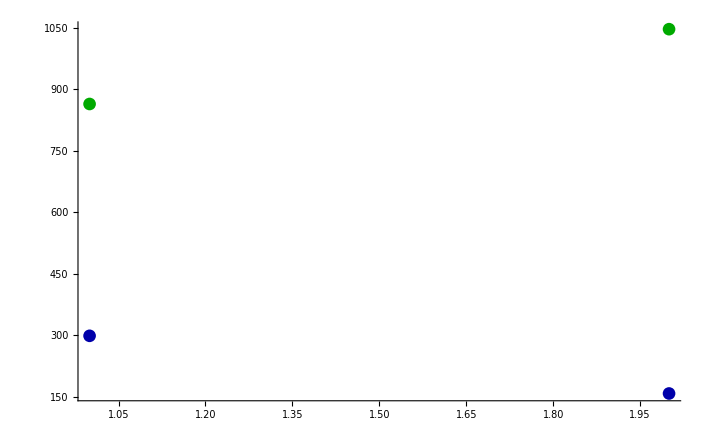

```mathematica
Show[DiscretePlot[{lbSY80p10t10m10sim [[x]],ubSY80p10t10m10sim [[x]]},{x,1,1},Filling->{1->{2}},PlotStyle->{Blue,Blue},ExtentSize->0.7],DiscretePlot[{TestSY10t10m1kJune17[[x]],TrainSY10t10m1kJune17[[x]]},{x,1,2},Filling->None,PlotStyle->{Darker[Green],Darker[Blue]},PlotRange->All],PlotRange->All,Axes->{False,True}]
```

Part::partw: Part 3 of {0,0} does not exist.

Part::partw: Part 4 of {0,0} does not exist.

Part::partw: Part 3 of {0.,0.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

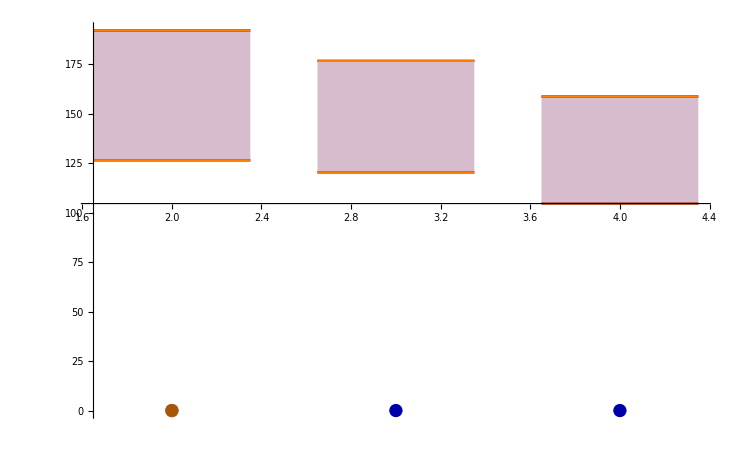

```mathematica
Show[DiscretePlot[{lbLC80p10t6m100sim[[x]],ubLC80p10t6m100sim[[x]],lbLC80p10t6m100sim[[x]],ubLC80p10t6m100sim[[x]]},{x,2,4},Filling->{1->{2},3->{4}},PlotStyle->{Blue,Blue,Orange,Orange},ExtentSize->0.7],DiscretePlot[{TestingLossLC[[x]],TrainingLossLC[[x]],TestingLossSY[[x]],TrainingLossSY[[x]]},{x,2,4},Filling->None,PlotStyle->{Lighter[Lighter[Lighter[Blue]]],Darker[Blue],Lighter[Lighter[Lighter[Orange]]],Darker[Orange]},PlotRange->All],PlotRange->All,Axes->{False,True}]
```

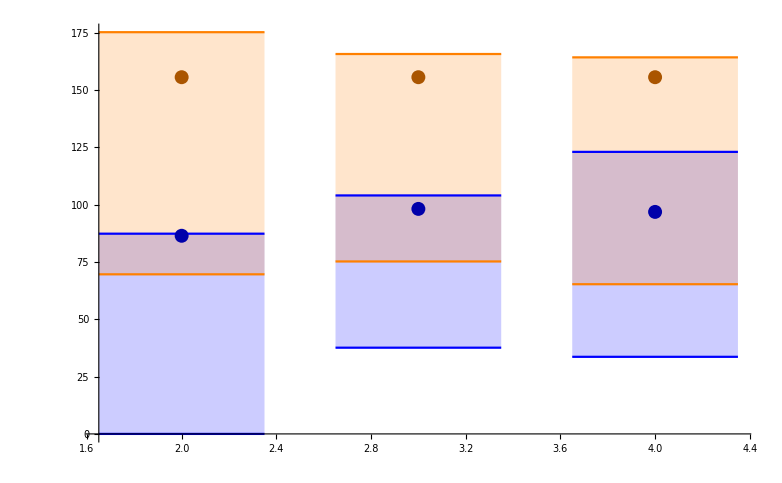

```mathematica
Show[DiscretePlot[{diflbLC80p10t4m100sim[[x]],difubLC80p10t4m100sim[[x]],diflbSY80p10t4m100sim[[x]],difubSY80p10t4m100sim[[x]]},{x,2,4},Filling->{1->{2},3->{4}},PlotStyle->{Blue,Blue,Orange,Orange},ExtentSize->0.7],DiscretePlot[{TestingLossLC[[x]]-TrainingLossLC[[x]],TestingLossSY[[x]]-TrainingLossSY[[x]]},{x,2,4},Filling->None,PlotStyle->{Darker[Blue],Darker[Orange]},PlotRange->All],PlotRange->All,Axes->{False,True}]
```

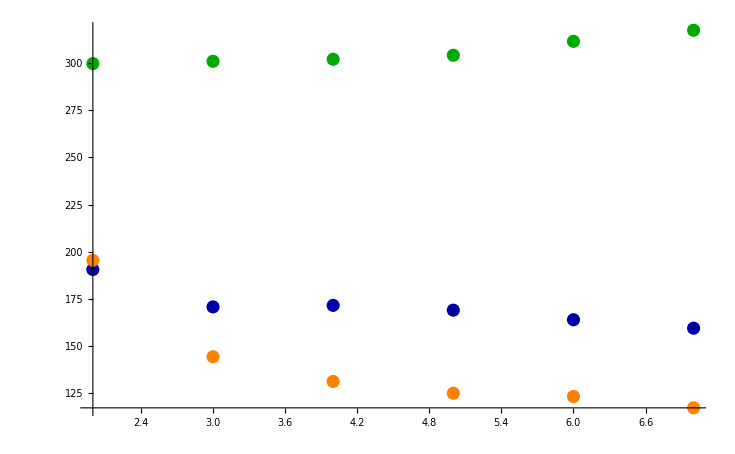

```mathematica
DiscretePlot[{TestingLossLC[[x]],TrainingLossLC[[x]],[[x]]},{x,2,7},Filling->None,PlotStyle->{Darker[Green],Darker[Blue],Orange},PlotRange->All]
```

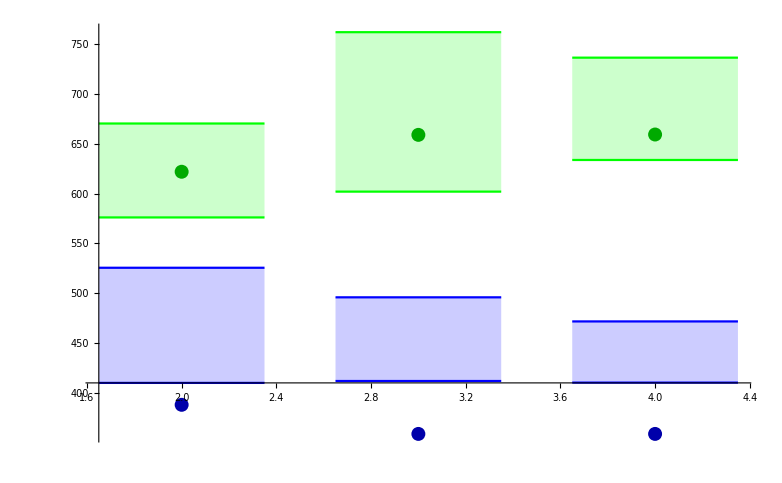

```mathematica
Show[DiscretePlot[{lbTE[[x]],ubTE[[x]],lbTR[[x]],ubTR[[x]]},{x,2,4},Filling->{1->{2},3->{4}},PlotStyle->{Green,Green,Blue,Blue},ExtentSize->0.7],DiscretePlot[{TestingLossLC[[x]],TrainingLossLC[[x]]},{x,2,4},Filling->None,PlotStyle->{Darker[Green],Darker[Blue]},PlotRange->All],PlotRange->All,Axes->{False,True}]
```

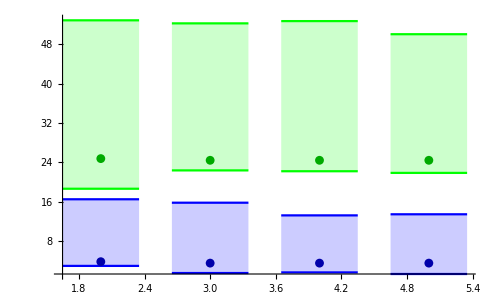

```mathematica
Show[DiscretePlot[{lbTE[[x]],ubTE[[x]],lbTR[[x]],ubTR[[x]]},{x,2,5},Filling->{1->{2},3->{4}},PlotStyle->{Green,Green,Blue,Blue},ExtentSize->0.7,PlotRange->All],DiscretePlot[{TestingLossLC[[x]],TrainingLossLC[[x]]},{x,2,5},Filling->None,PlotStyle->{Darker[Green],Darker[Blue]},PlotRange->All],PlotRange->All]
```

```mathematica
listtemp = BinCounts[ErrorPlayTR,{0,Ceiling[Max[ErrorPlayTR]],1}]
Flatten[Position[listtemp,Max[listtemp]]][[1]]
```

{1,4,12,30,40,51,67,55,53,70,62,76,60,49,45,43,40,25,27,28,21,15,23,16,9,14,14,8,9,9,0,3,1,3,3,1,2,3,3,1,1,1,1,0,0,1}

12

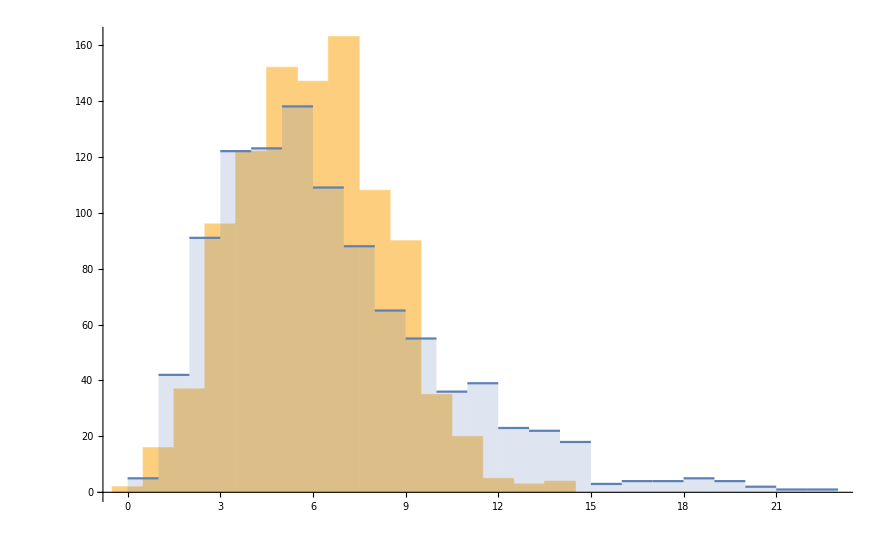

```mathematica
Show[Histogram[RandomVariate[PoissonDistribution[Flatten[Position[listtemp,Max[listtemp]]][[1]]/2],1000]],ListStepPlot[BinCounts[ErrorPlayTR,{0,Ceiling[Max[ErrorPlayTR]],2}],Left,Joined->False,Filling->Bottom],PlotRange->All]
```

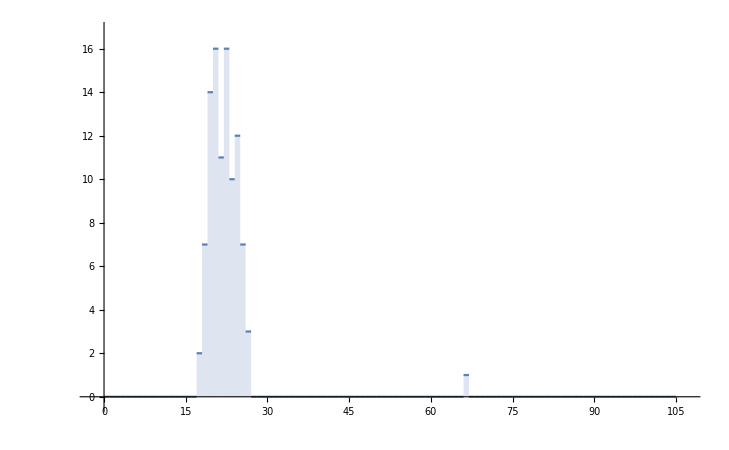

```mathematica
ListStepPlot[BinCounts[TRerrorLC[[4]],{0,Ceiling[Max[TRerrorLC[[4]]]],20}],Left,Joined->False,Filling->Bottom]
```

```mathematica
Mean[TRerrorLC[[4]]]
```

463.819

```mathematica
ubLC80p10t10m100sim
lbLC80p10t10m100sim
```

{551.44,548.27,534.7,533.36,473.68}

{424.56,442.64,395.74,388.72,366.72}

```mathematica
ubLC80p10t10m100sim
lbLC80p10t10m100sim
```

{585.6,548.27,534.67,510.76,469.86}

{439.2,437.61,399.95,379.68,366.72}

```mathematica
num=0;
Do[
If[TRerrorLC[[3]][[i]]>517,num = num+1]
,{i,1,Length[TRerrorLC[[4]]]}]
num
```

```mathematica
TRerrorSY[[2]]
```

{224.113,391.339,159.423,0,0,0,0,0,0,0}

```mathematica
Mean[Transpose[TRerrorSY]]
```

{306.153,77.4875,0}

```mathematica
num = 0;
Do[
If[TRerrorLC[[3]][[i]]<378,num = num+1]
,{i,1,Length[TRerrorLC[[4]]]}]
num
```

3

### Fitting

```mathematica
LossClassicalStdDev[ Model_,trainingfilename_,testfilename_,K_,Niter_,Nboot_,OG_] :=Module[{err,Err,newrhoout,Peturbcounts,tempFid,rhoout,errlist,Errlist,rawcountsTE,rawcountsTR,rawanglesTE,rawanglesTR,PavgTE,PavgTR,WeightTE,WeightTR,UvecFit,PeturbcountsTR,PeturbcountsTE,temperr,PPavgTR,PWeightTR,tempErr,M},
Clear[PavgTE,PavgTR,WeightTR,WeightTE,M,tempErr,Errlist,errlist];
{rawcountsTR,rawanglesTR,g2TR,{η1TR,η2TR,η3TR,η4TR}} = ReadCounts[trainingfilename];
{rawcountsTE,rawanglesTE,g2TE,{η1TE,η2TE,η3TE,η4TE}} = ReadCounts[testfilename];
countsTR = AvgCountsOntoTrans2[rawcountsTR];
{PavgTR,WeightTR,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTR]];
{PavgTE,WeightTE,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTE]];
If[OG==True,
{err,UvecFit} = CausalFit[ Model,"LS",PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
Err= CostCal["LS",PavgTE,UvecFit,WeightTE,M];, err =0;Err=0;
];
errlist = {};
Errlist = {};
Print["Resampling..."];
Do[
PeturbcountsTR=ArrayReshape[PoisonPeturbList[countsTR],{Length[countsTR]/4,4}];
Clear[PavgTE,PavgTR,WeightTR,WeightTE,M];
{PPavgTR,PWeightTR,M}=WeightsANDProbs[PeturbcountsTR];
{PavgTE,WeightTE,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTE]];
{temperr,UvecFit} = CausalFit[ Model,"LS",PPavgTR,PWeightTR,K,M,"NelderMead",1, Niter];
tempErr= CostCal["LS",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed B= ",i];
AppendTo[errlist,temperr];
AppendTo[Errlist,tempErr];
,{i,1,Nboot}];
Return[{err,Sqrt[Variance[errlist]],Err,Sqrt[Variance[Errlist]],errlist,Errlist}];
];
```

```mathematica
PoisonPeturbArray[list_] := Module[{newlist,m,n,templist,newlistout,flatlist},
m = Dimensions[list][[1]];
n = Dimensions[list][[2]];
templist = ArrayReshape[list,{m*n,1}];
newlist = Flatten[templist];
flatlist = Flatten[templist];
Do[
newlist[[i]] = RandomVariate[PoissonDistribution[flatlist[[i]]]];
,{i,1,m}];
newlistout = ArrayReshape[newlist,{m,n}];
Return[newlistout];
];
```

```mathematica
LossQuantumStdDev[ trainingfilename_,testfilename_,Niter_,Nboot_] :=Module[{err,Err,newrhoout,Peturbcounts,tempFid,rhoout,errlist,Errlist,rawcountsTE,rawcountsTR,rawanglesTE,rawanglesTR,PavgTE,PavgTR,WeightTE,WeightTR,UvecFit,PeturbcountsTR,PeturbcountsTE,temperr,PPavgTR,PWeightTR,tempErr,M,PeturbrawcountsTR},
Clear[PavgTE,PavgTR,WeightTR,WeightTE,M,tempErr,Errlist,errlist,c,d,e,UvecFit,err,Err];
{rawcountsTR,rawanglesTR,g2TR,{η1TR,η2TR,η3TR,η4TR}} = ReadCounts[trainingfilename];
{rawcountsTE,rawanglesTE,g2TE,{η1TE,η2TE,η3TE,η4TE}} = ReadCounts[testfilename];
{PavgTR,WeightTR,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTR]];
{PavgTE,WeightTE,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTE]];
{err,UvecFit,c,d,e}=QuantumLSout[M,PavgTR,WeightTR,1,Niter] ;
Err=CostCal["LS",PavgTE,UvecFit,WeightTE,M];
errlist = {};
Errlist = {};
Print["Resampling..."];
Do[
Clear[c,d,e,PavgTR,WeightTR,M];
PeturbrawcountsTR = PoisonPeturbArray[rawcountsTR];
{PPavgTR,PWeightTR,M}=WeightsANDProbs[AvgCountsOntoTrans[PeturbrawcountsTR]];
{temperr,UvecFit,c,d,e}=QuantumLSout[M,PPavgTR,PWeightTR,1,Niter] ;
tempErr =CostCal["LS",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed B= ",n];
AppendTo[errlist,temperr];
AppendTo[Errlist,tempErr];
,{n,1,Nboot}];
Return[{err,Sqrt[Variance[errlist]],Err,Sqrt[Variance[Errlist]],errlist,Errlist}];
];
```

```mathematica
KminLC = 1;
KmaxLC =20;
KminSY = 1;
KmaxSY=3;
SimCausal = True;
(*trainingfilename ="/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_localcausal_Jun21_6meas_2K_10000Totalcounts_0DarkCounts_1TR.txt";
testfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedCausal/sim_localcausal_Jun21_6meas_2K_10000Totalcounts_0DarkCounts_1TE.txt";*)
(*SimCausal = False;
trainingfilename ="/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedData/expsim_Jul22_6meas_10000Totalcounts_5DarkCounts_25._depol_1.txt";
testfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/SimulatedData/expsim_Jul22_6meas_10000Totalcounts_5DarkCounts_25._depol_2.txt";*)
SimCausal = False;
(*trainingfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul6_6meas_500cc_LCRX_P500ms_5R_10s_1.txt";
testfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul6_6meas_500cc_LCRX_P500ms_5R_10s_2.txt";*)
trainingfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt";
testfilename = "/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt";
Clear[PavgTE,PavgTR,WeightTR,WeightTE,M];
TestingLossLC = ConstantArray[0,KmaxLC];
TrainingLossLC = ConstantArray[0,KmaxLC];
TestingLossSY = ConstantArray[0,KmaxSY];
TrainingLossSY= ConstantArray[0,KmaxSY];
{rawcountsTR,rawanglesTR,g2TR,{η1TR,η2TR,η3TR,η4TR}} = ReadCounts[trainingfilename];
{rawcountsTE,rawanglesTE,g2TE,{η1TE,η2TE,η3TE,η4TE}} = ReadCounts[testfilename];
EffectsTE = WPAngles[rawanglesTE];
If[SimCausal,
{PavgTR,WeightTR,M}=WeightsANDProbs[rawcountsTR];
{PavgTE,WeightTE,M}=WeightsANDProbs[rawcountsTE];
,
{PavgTR,WeightTR,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTR]];
{PavgTE,WeightTE,M}=WeightsANDProbs[AvgCountsOntoTrans[rawcountsTE]];]
```

Do the local causal Fit

```mathematica
{err,UvecFit,Par} = CausalFitParameter[ "SY","LS",PavgTR,WeightTR,2,M,"NelderMead",1, 20];
Err= CostCal["LS",PavgTE,UvecFit,WeightTE,M];
```

```mathematica
Print[err,UvecFit,Err,Par]
```

0.000302155{{0.492058,0.00521064,0.00873951,0.493992},{0.387408,0.10986,0.112019,0.390713},{0.282049,0.21522,0.215545,0.287186},{0.204438,0.29283,0.287354,0.215377},{0.114563,0.382706,0.392128,0.110604},{0.00690817,0.49036,0.494436,0.00829604},{0.393927,0.099458,0.107445,0.39917},{0.196866,0.296519,0.303187,0.203429},{0.3532,0.140185,0.13931,0.367305},{0.391054,0.10233,0.108634,0.397981},{0.0695603,0.423824,0.440381,0.0662342},{0.0999775,0.393407,0.39965,0.106965},{0.309357,0.187783,0.191568,0.311291},{0.375272,0.121869,0.125242,0.377618},{0.475221,0.0219193,0.0249123,0.477947},{0.149684,0.347456,0.344693,0.158167},{0.0588424,0.438298,0.446489,0.0563709},{0.189953,0.307187,0.317371,0.185489},{0.198409,0.308634,0.298384,0.194573},{0.398396,0.108647,0.103834,0.389122},{0.152751,0.354292,0.344267,0.14869},{0.0450351,0.462008,0.450259,0.0426979},{0.391277,0.115766,0.113914,0.379043},{0.308595,0.198448,0.191379,0.301578},{0.0951311,0.400581,0.409251,0.0950364},{0.0628947,0.432818,0.44228,0.0620073},{0.0655066,0.430206,0.431124,0.0731631},{0.37846,0.117253,0.114322,0.389965},{0.442637,0.0530751,0.0573238,0.446964},{0.400287,0.0954254,0.0930831,0.411204},{0.0075192,0.488642,0.495785,0.00805439},{0.114527,0.381634,0.394055,0.109784},{0.212349,0.283811,0.286325,0.217514},{0.284258,0.211903,0.207686,0.296153},{0.385822,0.110339,0.112643,0.391196},{0.49133,0.00483057,0.0112763,0.492563}}0.00275417{a[1]→0.00637493,a[2]→0.993773,a[3]→0.0526091,a[4]→0.939199,a[5]→0.0438401,a[6]→0.955623,a[7]→0.939189,a[8]→0.0699574,a[9]→0.952045,a[10]→0.0341636,a[11]→0.00001001,a[12]→0.997984,b[1]→0.0113215,b[2]→0.219351,b[3]→0.427885,b[4]→0.572586,b[5]→0.783422,b[6]→0.989545,b[7]→0.17263,b[8]→0.611875,b[9]→0.245315,b[10]→0.175527,b[11]→0.918266,b[12]→0.82831,b[13]→0.369346,b[14]→0.22472,b[15]→0.00592785,b[16]→0.703961,b[17]→0.924929,b[18]→0.643115,b[19]→0.374423,b[20]→0.831099,b[21]→0.269926,b[22]→0.023761,b[23]→0.814338,b[24]→0.626005,b[25]→0.168779,b[26]→0.098876,b[27]→0.105167,b[28]→0.783502,b[29]→0.922019,b[30]→0.83075,b[31]→0.985945,b[32]→0.783205,b[33]→0.568567,b[34]→0.411886,b[35]→0.222465,b[36]→0.0204512,b[37]→0.995868,b[38]→0.782705,b[39]→0.5681,b[40]→0.410075,b[41]→0.226796,b[42]→0.007562,b[43]→0.833871,b[44]→0.386952,b[45]→0.74253,b[46]→0.827555,b[47]→0.096949,b[48]→0.167188,b[49]→0.63401,b[50]→0.779459,b[51]→0.999989,b[52]→0.282397,b[53]→0.0809366,b[54]→0.36998,b[55]→0.620562,b[56]→0.169603,b[57]→0.726705,b[58]→0.972217,b[59]→0.192511,b[60]→0.372502,b[61]→0.843822,b[62]→0.916118,b[63]→0.89257,b[64]→0.198738,b[65]→0.0730784,b[66]→0.152134,b[67]→0.0151449,b[68]→0.230821,b[69]→0.427984,b[70]→0.572916,b[71]→0.77762,b[72]→0.990274,c[1]→0.631682,c[2]→0.624542}

```mathematica
Clear[c,d,e];
{TrainingLossQ,UvecFit,c,d,e}=QuantumLSout[M,PavgTR,WeightTR,1,20] ;
TestingLossQ =CostCal["LS",PavgTE,UvecFit,WeightTE,M];
TrainingLossQ
TestingLossQ
```

0.0014964

0.0020752

```mathematica
LossQuantumStdDev["/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul6_6meas_500cc_LCRX_P500ms_5R_10s_1.txt","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul6_6meas_500cc_LCRX_P500ms_5R_10s_2.txt",20,10]
```

Resampling...

Completed B= 1

Completed B= 2

Completed B= 3

Completed B= 4

Completed B= 5

Completed B= 6

Completed B= 7

Completed B= 8

Completed B= 9

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 40000 iterations.

Completed B= 10

{0.0014964,0.0000984858,0.0020752,0.0000819429,{0.001447,0.00166066,0.00173059,0.0016415,0.00180965,0.00170924,0.00164027,0.00173412,0.00166498,0.00158307},{0.00203682,0.00208522,0.00217464,0.00208529,0.0022747,0.00211635,0.00212555,0.00214024,0.00219357,0.00198456}}

```mathematica
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "SY","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt",20,0,True];
Print[err,stderr,Err,stdErr]
```

Set::shape: Lists {err,stderr,Err,stdErr,errlist,Errlist} and LossClassicalStdDev[SY,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt,20,0,True] are not the same shape.

errstderrErrstdErr

```mathematica
errlist
```

{0.0533236,0.00167915,0.574532,0.00166254,0.574271,0.00147937,0.341942,0.186701,0.00150249,0.539447}

```mathematica
StandardDeviation[{0.007445325325250875,0.0016658113308125233,0.0016204571804114753,0.0015863864344972335}]
```

0.00291074

```mathematica
Do[
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "SD","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt",i,20,10];
Print[err,stderr,Err,stdErr]
,{i,1,12}]
```

Set::shape: Lists {err,stderr,Err,stdErr,errlist,Errlist} and LossClassicalStdDev[SD,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt,1,20,10] are not the same shape.

errstderrErrstdErr

Set::shape: Lists {err,stderr,Err,stdErr,errlist,Errlist} and LossClassicalStdDev[SD,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt,2,20,10] are not the same shape.

errstderrErrstdErr

Set::shape: Lists {err,stderr,Err,stdErr,errlist,Errlist} and LossClassicalStdDev[SD,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt,/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt,3,20,10] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

```mathematica
Do[Print[i],{i,1,10,2}]
```

1

3

5

7

9

```mathematica
Do[
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "SD","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_1.txt","/Users/patrickdaley/Google Drive/Documents/IQCMasters/GPTBell/Bell2019/LabData/jul8_6meas_500cc_LCRid_10s_2.txt",i,20,5,False];
Print["Tr: ",err," +- ",stderr,"     TE: ",Err," +- ",stdErr]
,{i,10,12,2}]
```

Resampling...

Completed B= 1

Completed B= 2

Completed B= 3

Completed B= 4

Completed B= 5

Tr: 0 +- 0.0000555235     TE: 0 +- 0.000287401

Resampling...

$Aborted

```mathematica
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "SD",trainingfilename,testfilename,2,1,5];
Print[err,stderr,Err,stdErr]
```

$Aborted

0.001504430.01269310.002065960.0106797

```mathematica
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "LC",trainingfilename,testfilename,1,1,5];
Print[err,stderr,Err,stdErr]
```

Resampling...

Completed B= 1

Completed B= 2

Completed B= 3

Completed B= 4

Completed B= 5

0.7530010.003094060.7398390.000195129

```mathematica
{err,stderr,Err,stdErr,errlist,Errlist}=LossClassicalStdDev[ "SD",trainingfilename,testfilename,4,5,5];
Print[err,stderr,Err,stdErr]
```

Resampling...

Completed B= 1

Completed B= 2

Completed B= 3

Completed B= 4

Completed B= 5

Completed B= 6

Completed B= 7

Completed B= 8

Completed B= 9

Completed B= 10

Completed B= 11

Completed B= 12

Completed B= 13

Completed B= 14

Completed B= 15

Completed B= 16

Completed B= 17

Completed B= 18

Completed B= 19

Completed B= 20

0.001063170.0001623540.00229270.000242248

```mathematica
stdErr
```

0.000046608

```mathematica
Err
```

0.739839

```mathematica
Model = "SY";
Loss = "LS";
Niter= 20;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,1,4}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

{3.27512,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{3.26803,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 2

{3.27512,0.000302155,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{3.26803,0.00275417,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 3

{3.27512,0.000302155,0.000302155,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{3.26803,0.00275417,0.00275417,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

$Aborted

{3.27512,0.000302155,0.000302155,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{3.26803,0.00275417,0.00275417,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "SY";
Loss = "LS";
Niter= 20;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,1,4}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

{0.751672,-338.281,-515.015,-942.431,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{0.741152,-349.651,-533.439,-857.935,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 2

{0.751672,0.000195293,-515.015,-942.431,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{0.741152,0.00350377,-533.439,-857.935,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 3

{0.751672,0.000195293,0.000195293,-942.431,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{0.741152,0.00350377,0.00350377,-857.935,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 4

{0.751672,0.000195293,0.000195293,0.000195293,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{0.741152,0.00350377,0.00350377,0.00350377,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0.751672,0.000195293,0.000195293,0.000195293,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{0.741152,0.00350377,0.00350377,0.00350377,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "SD";
Loss = "MLE";
Niter= 20;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,1,6}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

{-40.7983,26152.3,7613.76,274.933,87.7476,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{-43.343,23752.5,6541.83,583.189,857.56,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 2

{-40.7983,-338.281,7613.76,274.933,87.7476,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{-43.343,-349.651,6541.83,583.189,857.56,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 3

{-40.7983,-338.281,-515.015,274.933,87.7476,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{-43.343,-349.651,-533.439,583.189,857.56,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 4

{-40.7983,-338.281,-515.015,-942.431,87.7476,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{-43.343,-349.651,-533.439,-857.935,857.56,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 5

{-40.7983,-338.281,-515.015,-942.431,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{-43.343,-349.651,-533.439,-857.935,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

$Aborted

{-40.7983,-338.281,-515.015,-942.431,-1010.68,67.3281,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{-43.343,-349.651,-533.439,-857.935,-862.666,882.906,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "SD";
Loss = "WLS";
Niter= 5;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,6,6}];
TrainingLossLC
TestingLossLC
```

Completed K= 4

{17.4757,5.5932,2.75804,-120.76,0.284011,0.0200511,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{17.4234,5.58894,2.71821,-122.024,0.278969,0.0244185,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 5

{17.4757,5.5932,2.75804,-120.76,-290.354,0.0200511,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{17.4234,5.58894,2.71821,-122.024,-285.512,0.0244185,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 6

{17.4757,5.5932,2.75804,-120.76,-290.354,-317.835,0,0,0,0,0,0,0,0,0,0,0,0,0,0}{17.4234,5.58894,2.71821,-122.024,-285.512,-319.074,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{17.4757,5.5932,2.75804,-120.76,-290.354,-317.835,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{17.4234,5.58894,2.71821,-122.024,-285.512,-319.074,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "SD";
Loss = "MLE";
Niter= 20;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];.
,{K,6,6}];
TrainingLossLC
TestingLossLC
```

```mathematica
Model = "SD";
Loss = "WLSe";
Niter= 20;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",1, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,1,6}];
TrainingLossLC
TestingLossLC
```

Completed K= 9

{0,0,0,0,0,0,0,0,0.000345278,0,0,0,0,0,0,0,0,0,0,0}{0,0,0,0,0,0,0,0,0.00264113,0,0,0,0,0,0,0,0,0,0,0}

Completed K= 10

{0,0,0,0,0,0,0,0,0.000345278,0.000435475,0,0,0,0,0,0,0,0,0,0}{0,0,0,0,0,0,0,0,0.00264113,0.00250066,0,0,0,0,0,0,0,0,0,0}

Completed K= 11

{0,0,0,0,0,0,0,0,0.000345278,0.000435475,0.000334622,0,0,0,0,0,0,0,0,0}{0,0,0,0,0,0,0,0,0.00264113,0.00250066,0.00267916,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0.000345278,0.000435475,0.000334622,0,0,0,0,0,0,0,0,0}

{0,0,0,0,0,0,0,0,0.00264113,0.00250066,0.00267916,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "LC";
Loss = "LS";
Niter= 60;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",21, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,11,12}];
TrainingLossLC
TestingLossLC
```

$Aborted

{0.753001,0.0995304,0.0294298,0.00146673,0.00139575,0.00138296,0.00138279,0.00138279,0,0,0,0,0,0,0,0,0,0,0,0}

{0.739839,0.0918911,0.0255474,0.00201981,0.00206802,0.00211197,0.00211351,0.00211351,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Model = "SD";
Loss = "LS";
Niter= 60;
HiddenDim = 3;
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ Model,Loss,PavgTR,WeightTR,K,M,"NelderMead",21, Niter];
TestingLossLC[[K]] =CostCal[Loss,PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
Print[TrainingLossLC,TestingLossLC];
item = PrintTemporary["Running..."];
,{K,1,10}];
TrainingLossLC
TestingLossLC
```

Completed K= 2

{3.2764,0.923388,0.448575,0,0.15823,0,0,0,0,0,0,0.102946,0.0819922,0.0793103,0.0816353,0,0,0,0,0}{3.26659,0.925138,0.444091,0,0.159563,0,0,0,0,0,0,0.102125,0.0827638,0.0797237,0.0825988,0,0,0,0,0}

{3.2764,0.923388,0.448575,0,0.15823,0,0,0,0,0,0,0.102946,0.0819922,0.0793103,0.0816353,0,0,0,0,0}

{3.26659,0.925138,0.444091,0,0.159563,0,0,0,0,0,0,0.102125,0.0827638,0.0797237,0.0825988,0,0,0,0,0}

```mathematica
(************** end of recent sims************)
```

```mathematica
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ "LC","MLE",PavgTR,WeightTR,K,M,"NelderMead",1, 20];
TestingLossLC[[K]] =CostCal["MLE",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,KminLC,KmaxLC}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

Completed K= 2

Completed K= 3

Completed K= 4

Completed K= 5

{-40.7983,-338.114,-513.814,-945.125,-945.733}

{-43.343,-349.571,-534.19,-899.752,-897.723}

```mathematica
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ "SY","WLS",PavgTR,WeightTR,K,M,"NelderMead",1, 20];
TestingLossLC[[K]] =CostCal["WLS",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,KminLC,KmaxLC}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

Completed K= 2

Completed K= 3

Completed K= 4

Completed K= 5

{4.01368,0.00107165,0.00107165,0.00107165,0.00107165}

{3.95782,0.019127,0.019127,0.019127,0.019127}

```mathematica
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ "SY","LS",PavgTR,WeightTR,K,M,"NelderMead",1, 20];
TestingLossLC[[K]] =CostCal["LS",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,1,2}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

Completed K= 2

{0.751672,0.000195293,52.2123,52.2123,0.00107165}

{0.741152,0.00350377,890.806,890.806,0.019127}

```mathematica
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ "SY","WLS",PavgTR,WeightTR,K,M,"NelderMead",1, 20];
TestingLossLC[[K]] =CostCal["WLS",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,1,2}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

Completed K= 2

{4.01368,0.00107165,52.2123,52.2123,0.00107165}

{3.95782,0.019127,890.806,890.806,0.019127}

```mathematica
Do[
Clear[UvecFit];
{TrainingLossLC[[K]],UvecFit} = CausalFit[ "SY","MLE",PavgTR,WeightTR,K,M,"NelderMead",1, 20];
TestingLossLC[[K]] =CostCal["MLE",PavgTE,UvecFit,WeightTE,M];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,1,2}];
TrainingLossLC
TestingLossLC
```

Completed K= 1

Completed K= 2

{-41.0479,-1234.97,52.2123,52.2123,0.00107165}

{-43.0681,-819.971,890.806,890.806,0.019127}

Quantum Fits. The first

```mathematica
Clear[UvecFitQ];
{TrainingLossQ,UvecFitQ} =QuantumMLE[M,PavgTR,WeightTR,50];
TestingLossQ = Total[Total[(PavgTE-UvecFitQ)^2*WeightTE]];
TrainingLossQ
TestingLossQ
```

$Aborted

1332.77

Do the SY causal structure fit over the range of hidden variable dimensions specified.

```mathematica
item = PrintTemporary["Running..."];
Do[
{TrainingLossSY[[K]],UvecFit} = SuperluminalSYMLEIter[K,M,PavgTR,WeightTR,50,"NelderMead",1];
TestingLossSY[[K]] = Total[Total[(PavgTE-UvecFit)^2*WeightTE]];
Clear[UvecFit];
NotebookDelete[item];
Print["Completed K= ",K];
item = PrintTemporary["Running..."];
,{K,KminSY,KmaxSY}];
TrainingLossSY
TestingLossSY
Speak["SY causal fit is done for simulated lab data"];
```

Some plots of the data.

```mathematica
TrainingLossLCEntJul8 = {};
TestingLossLCEntJul8 = {};
TrainingLossSYEntJul8={};
TestingLossSYEntJul8 = {};
TRQEntJul8 =  ConstantArray[,10];
TEQEntJul8 =  ConstantArray[,10];
```

```mathematica
Show[DiscretePlot[{TrainingLossLCEntJul8[[k]],TestingLossLCEntJul8[[k]]},{k,1,6},PlotLegends -> {"TrainingLC","TestingLC"},PlotRange->{0,1000},Filling->None,Joined->True,PlotStyle->{{Dashed,RGBColor["#88A2AA"]},{Thick,RGBColor["#88A2AA"]}},PlotLabel->"expsim_Jun17_10meas_10000Totalcounts_5DarkCounts_alpha0.840896_MixedFalse_1",AxesLabel->{"Dim of HV","Errorr"}],
DiscretePlot[{TrainingLossSYEntJul8[[k]],TestingLossSYEntJul8[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Dashed,RGBColor["#FF784F"]},{Thick,RGBColor["#FF784F"]}}],
DiscretePlot[{TRQEntJul8[[k]],TEQEntJul8[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Dashed,Blue},{Thick,Blue}}],PlotRange->All]
```

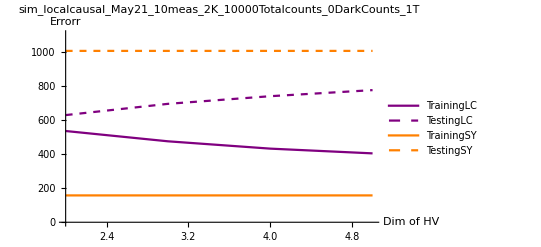

```mathematica
DiscretePlot[{TrainingLossLC[[k]],TestingLossLC[[k]],TrainingLossSY[[k]],TestingLossSY[[k]]},{k,2,5},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},PlotRange->{0,1100},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"sim_localcausal_May21_10meas_2K_10000Totalcounts_0DarkCounts_1T",AxesLabel->{"Dim of HV","Errorr"}]
```

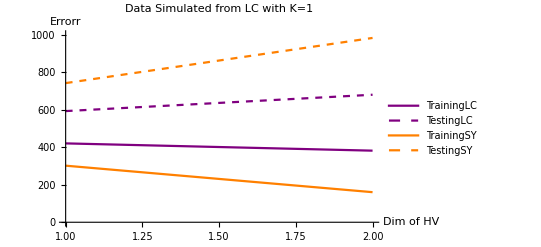

```mathematica
DiscretePlot[{TrainingLossLC[[k]],TestingLossLC[[k]],TrainingLossSY[[k]],TestingLossSY[[k]]},{k,1,2},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},PlotRange->{0,1000},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"Data Simulated from LC with K=1",AxesLabel->{"Dim of HV","Errorr"}]
```

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

545.348

1177.06

{493242.,187543.,103995.,50705.3,38686.4,32901.6,31863.2,24609.8}

{463169.,182988.,99879.,49805.1,37900.8,32547.2,31439.8,24169.6}

{430889.,271.02,192.768,192.768,0,0,0,0}

{408813.,1582.79,1363.32,1363.32,0,0,0,0}

```mathematica
TRQS = ConstantArray[TrainingLossQ,6];
TEQS = ConstantArray[TestingLossQ,6];
TrainingLossSY
```

{850205.,106684.,4834.65,18268.7,1478.63,209.831}

```mathematica
TrainingLossQ
TestingLossQ
```

460.483

688.63

```mathematica
TRQS = {423.607,423.607,423.607,423.607,423.607};
TEQS = {685.206,685.206,685.206,685.206,685.206,685.206};
TRLCS = {580.2234365423169,479.0852791332775,528.1676951479631,460.011684770718,511.5441457646021};
TELCS={717.0485506569759,677.2306442407487,729.8293494260101,671.3875447596562,663.2554109743139};
TRSYS = {372.63481698237814,340.8641576659478};
TESYS = {897.0433707386521,907.4688187185338};
```

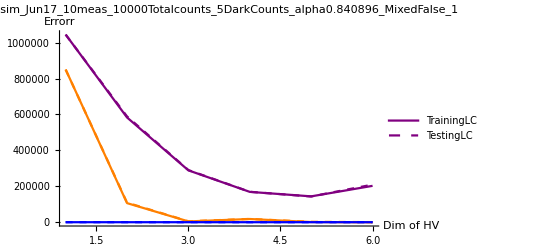

```mathematica
Show[DiscretePlot[{TrainingLossLCEXP10meas10tJune17[[k]],TestingLossLCEXP10meas10tJune17[[k]]},{k,1,6},PlotLegends -> {"TrainingLC","TestingLC"},PlotRange->{0,1000},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple}},PlotLabel->"expsim_Jun17_10meas_10000Totalcounts_5DarkCounts_alpha0.840896_MixedFalse_1",AxesLabel->{"Dim of HV","Errorr"}],
DiscretePlot[{TrainingLossSYEXP10meas10tJune17[[k]],TestingLossSYEXP10meas10tJune17[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Thick,Orange},{Dashed,Orange}}],
DiscretePlot[{TRQS[[k]],TEQS[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Thick,Blue},{Dashed,Blue}}],PlotRange->All]
```

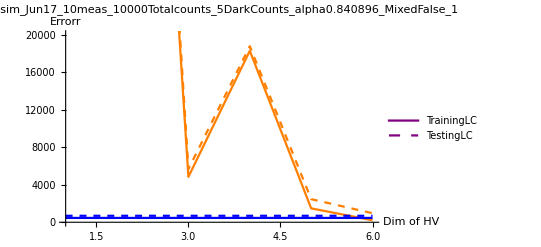

```mathematica
Show[DiscretePlot[{TrainingLossLCEXP10meas10tJune17[[k]],TestingLossLCEXP10meas10tJune17[[k]]},{k,1,4},PlotLegends -> {"TrainingLC","TestingLC"},PlotRange->{0,1000},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple}},PlotLabel->"expsim_Jun17_10meas_10000Totalcounts_5DarkCounts_alpha0.840896_MixedFalse_1",AxesLabel->{"Dim of HV","Errorr"}],
DiscretePlot[{TrainingLossSYEXP10meas10tJune17[[k]],TestingLossSYEXP10meas10tJune17[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Thick,Orange},{Dashed,Orange}}],
DiscretePlot[{TRQS[[k]],TEQS[[k]]},{k,1,6},Filling->None,Joined->True,PlotStyle->{{Thick,Blue},{Dashed,Blue}}],PlotRange->{0,20000}]
```

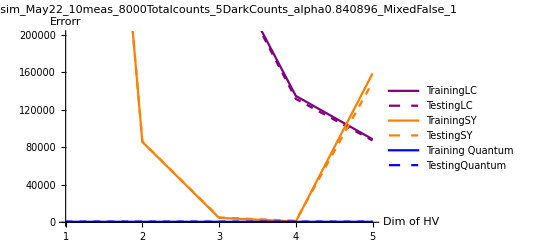

```mathematica
DiscretePlot[{TrainingLossLC[[k]],TestingLossLC[[k]],TrainingLossSY[[k]],TestingLossSY[[k]],TRQE[[k]],TEQE[[k]]},{k,1,6},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY","Training Quantum", "TestingQuantum"},PlotRange->{0,200000},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange},{Thick,Blue},{Dashed,Blue}},PlotLabel->"expsim_May22_10meas_8000Totalcounts_5DarkCounts_alpha0.840896_MixedFalse_1",AxesLabel->{"Dim of HV","Errorr"}]
```

```mathematica
TRSYE
```

{1.02507×10^6,85593.2,4655.36,805.481,158519.}

```mathematica
TestingLossTX
```

{1.42856×10^6,1.07492×10^6,1.01164×10^6,964817.,0}

```mathematica
TrainingLossTX
```

{1.4153×10^6,1.07024×10^6,1.00859×10^6,960675.,0}

## Different Minimization Options

```mathematica
Do[
Clear[UvecFit];
{temp,UvecFit}=LocalCausalMLEtemp[3,10,PavgTR,WeightTR,seed=i,"NelderMead"];
TestingLoss = Total[Total[(PavgTE-UvecFit)^2*WeightTE]];
Print["TR: ",temp,"    TE: ",TestingLoss]
,{i,1,1}]
```

TR: 93654.6    TE: 94983.6

TR: 408047.    TE: 407923.

TR: 322136.    TE: 322878.

TR: 167148.    TE: 167429.

TR: 746910.    TE: 738797.

TR: 357085.    TE: 347665.

```mathematica
Clear[UvecFit];
{temp,UvecFit}=SuperluminalSYMLEIter[3,10,PavgTR,WeightTR,seed=8,"NelderMead"];
TestingLoss = Total[Total[(PavgTE-UvecFit)^2*WeightTE]];
Print["TR: ",temp,"    TE: ",TestingLoss]
```

TR: 90089.2    TE: 90474.8

```mathematica
Do[
Clear[UvecFit];
{temp,UvecFit}=LocalCausalMLEtemp[6,10,PavgTR,WeightTR,seed=i,"NelderMead"];
Print[temp]
,{i,9,12}]
```

436658.

119815.

710099.

297138.

```mathematica
Do[
Clear[UvecFit];
{temp,UvecFit}=LocalCausalMLEtemp[6,10,PavgTR,WeightTR,seed=i,"SimulatedAnnealing"];
Print[temp]
,{i,1,6}]
```

342388.

$Aborted

```mathematica
{temp,UvecFit}=LocalCausalMLEIter[6,10,PavgTR,WeightTR,6,"NelderMead"];
```

$Aborted

```mathematica
temp
```

1.04477×10^6

```mathematica
pytempLC={1044770.635565119,583391.6324509344,286861.6628362546,169093.61626362498,169093.615726099,144254.9602871923,144254.9613253037,93517.07193080045};
pytempSY = {850380.1680237709,41310.44385506396,5354.050252900143,2168.0401220479794,2375.655807820507,4734.351649011085,848.1494474229321,782.617810962285};
```

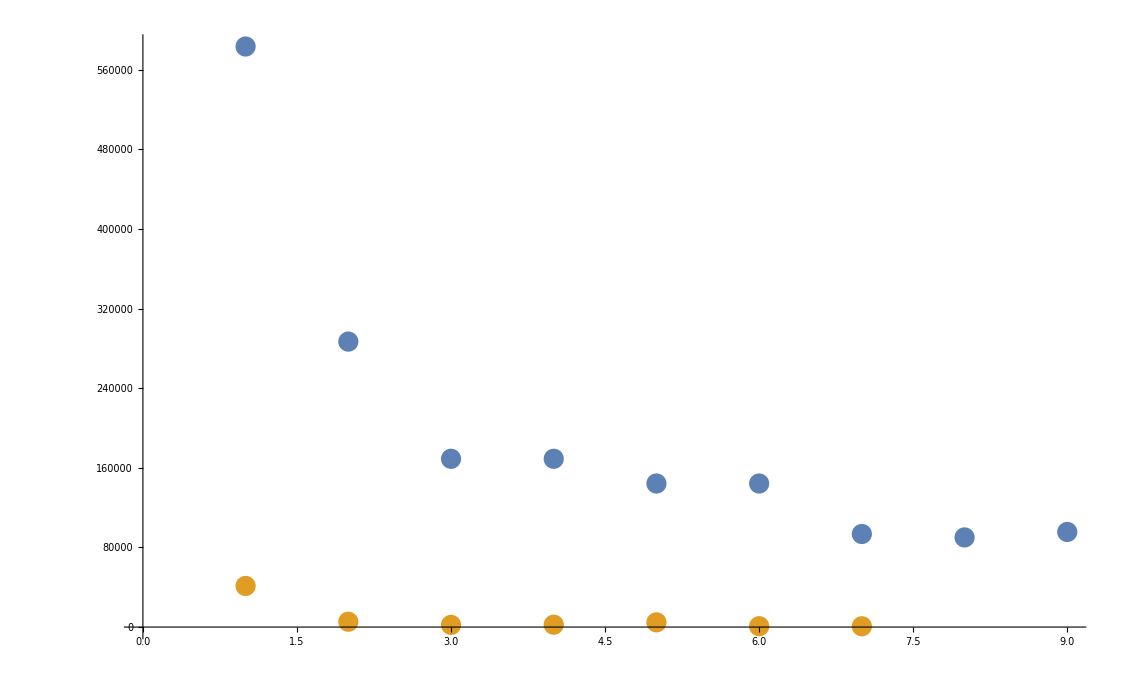

```mathematica
ListPlot[{pytempLCTR[[2;;]],pytempSY[[2;;]]}]
```

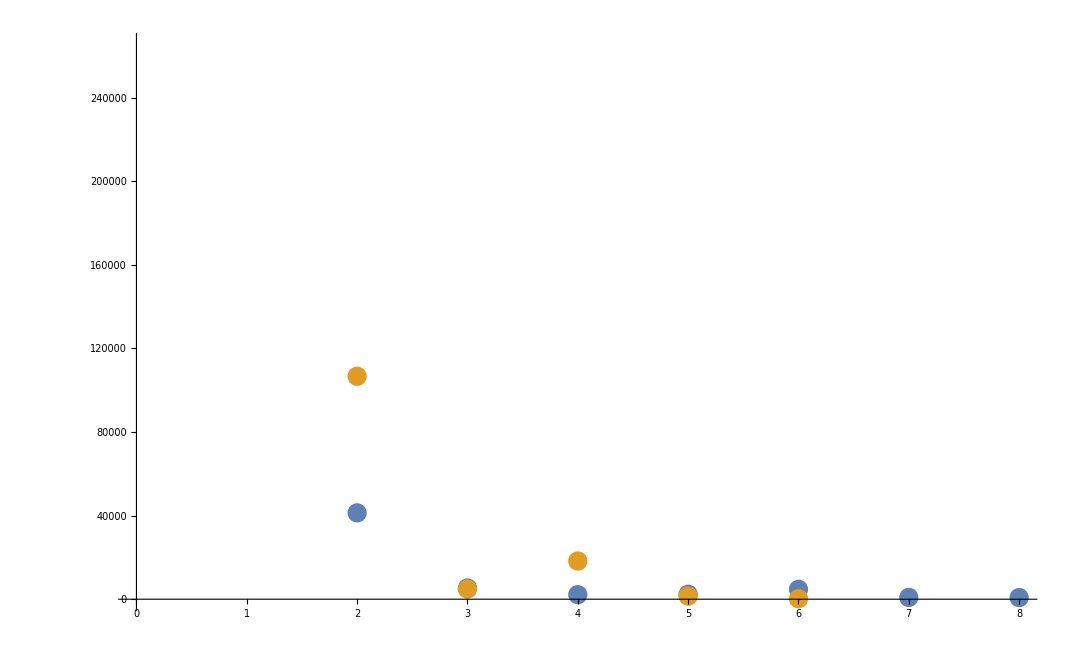

```mathematica
ListPlot[{pytempSY,TrainingLossSYEXP10meas10tJune17}]
```

```mathematica
pytempLCTE = {1044562.1395441454,589024.6358251986,289068.94452286663,171128.2709215294,171127.8023190992,143684.07393541533,143684.28963138832,94609.0610806341,90475.64012605163,95590.15918254157};
```

```mathematica
pytempSYout = [850380.1680237709,41310.44385506396,5354.050252900143,2168.0401220479794,2375.655807820507,4734.351649011085,848.1494474229321,782.617810962285][849917.1954273997,42927.22363483852,5790.275007211743,3383.627385154036,3489.0509401440977,5548.7393969441255,1689.6682541617888,1753.4822056380667] 9463.888527870178
```

```mathematica
TrainingLossLCEXP10meas10tJune17 = {1.0447706345941554*^6,583391.953149849,288962.6186116921,169247.8006515126,144269.19979967276,202825};
```

```mathematica
pytempLCTR={1044770.635565119,583391.6324509344,286861.6628362546,169093.61626362498,169093.615726099,144254.9602871923,144254.9613253037,93517.07193080045,90089.18324410265,95577.85808018522};
```

```mathematica
TrainingLossSYEXP10meas10tJune17 = {850204.7285529415,106684.23700863817,4834.650020343044,18268.718876286533,1478.6276947380575,209.83111463542693};
```

```mathematica
850380.1661500464,18893.85945358918,5324.484619558429,5127.59727422732,5473.55097610866,402.57963507290617
```

```mathematica
[850380.1661500464,18893.85945358918,5324.484619558429,5127.59727422732,5473.55097610866,402.57963507290617][849917.9590598869,18872.740531632844,5465.467341872546,5680.127305281278,5540.845016513528,1119.8374685259867] 14676.361552238464
```

```mathematica
LC STUFF here for 10 meas
```

```mathematica
working on K=9
working on K=10
[76405.97797119156,80966.67494602714][76353.04541784951,80178.79031747274] 7780.019222736359
```

## CurrentDATA for 2meas

```mathematica
m2SYk1LCTR = {9.654855417433252,3.8577153191582374,1.6076040907596525,1.607604090752267,1.60760409075635,1.6076040907419633,1.6076040907381988,1.607604090737755};
m2SYk1LCTE = {15.222478627116127,21.657627424619395,25.02905920238759,25.029077355861507,25.02908864014156,25.029079920475244,25.029084292387143,25.029084659027195};
m2SYk1SYTR = {8.48491769036874,0.6406579411606532,0.6406579409925653,0.6406579409487788,0.6406579409399147,0.6406579409467267,0.6406579409394789,0.6406579409363476};
m2SYk1SYTE = {15.117893182150175,24.51281050163402,24.512846694379824,24.512862091782893,24.512849077135773,24.51283993360729,24.51284809231837,24.512853879895637};
m2SYk2LCTR = {215.19633782047708,8.007346902943214,7.250864321497338,7.250864321498592,7.250864321495529,7.250864321494783,7.250864321494684,7.250864321494338};
m2SYk2LCTE = {241.34047939632163,22.907844968999083,23.946008927259026,23.945999305729483,23.94599992550628,23.946002621502338,23.946007028843532,23.946004987983933};
m2SYk2SYTR = {211.3330684755756,4.540415235706203,4.54041523570387,4.540415235704592,4.540415235704202,4.540415235702759,4.5404152357022145,4.540415235702294};
m2SYk2SYTE = {240.42454585330916,30.0298763022992,30.029876224298164,30.029865792035313,30.029874877413306,30.0298692049653,30.02986969172141,30.02987201676021};
m2SYk3LCTR = {937.7446440751994,2.363884638055808,2.0469600875517053,2.0469600875502634,2.046960087550661,2.0469600875499303,2.0469600875496536,2.0469600875495533};
m2SYk3LCTE= {1120.3483620601748,51.13424280926083,50.95615959716746,50.95615983278752,50.95617124105,50.95616826907805,50.95616671958234,50.95616377531144};
m2SYk3SYTR = {906.0990780626698,0.6170167772954982,0.6170167772983125,0.6170167772971786,0.6170167772972077,0.6170167772963846,0.6170167772964116,0.6170167772962788};
m2SYk3SYTE = {1089.5188860571166,50.42389722023391,50.42390907009133,50.423908078488566,50.423904360269205,50.42390390710763,50.4239035927228,50.423904197091474};
m2SYk4LCTR = {4549.039298530254,17.67353710500334,16.559994957088914,16.559994957085262,16.55999495708313,16.559994957082765,16.559994957082246,16.559994957082253};
m2SYk4LCTE = {4453.2789850662875,47.92164817456252,45.421720644082406,45.42171425778032,45.421714061522046,45.42171166346973,45.42171428794143,45.42171670244391};
m2SYk4SYTR = {4498.74072384903,8.062653994875124,8.062653994876145,8.06265399487577,8.062653994876614,8.062653994876385,8.062653994876209,8.06265399487544};
m2SYk4SYTE = {4392.552484651021,67.90018969126464,67.90018897617026,67.90018935078987,67.90019293226966,67.90018814769401,67.90019381902002,67.90018966089234};
m2LCk1LCTR = {4.280548869690678,2.4008162290097337,2.247019072255498,2.247019072257527,2.2470190722568866,2.24701907225648,2.2470190722561143,2.247019072256024};
m2LCk1LCTE = {24.231166725499108,25.957064134648178,26.158006086116398,26.158010902949208,26.15800469386424,26.158002937219635,26.158007368253248,26.158006944020205};
m2LCk1SYTR = {3.429478207605175,1.3681103842063445,1.368110384197717,1.3681103841952047,1.3681103841948044,1.3681103841948383,1.368110384194515,1.368110384194222};
m2LCk1SYTE = {26.12683202076281,27.791930769430067,27.791934041667318,27.79193302257582,27.791932190036405,27.791932430175333,27.79193431495115,27.791933397680122};
m2LCk2LCTR={1197.0218291939627,1.8971944068032827,1.894628148998597,1.8946281489995687,1.894628148999042,1.894628148998452,1.8946281489980872,1.8946281489978594};
m2LCk2LCTE = {1138.3939265189927,52.985319128916224,53.440205437253184,53.44019944922586,53.440189568686144,53.44019524937023,53.44019861497535,53.440192592258015};
m2LCk2SYTR = {1193.4297024083617,1.2863509029374431,1.2863509029372855,1.2863509029386166,1.2863509029368259,1.2863509029363653,1.2863509029361535,1.2863509029362727};
m2LCk2SYTE = {1125.7863534476564,47.43508123552442,47.43509012174674,47.4350910661012,47.4350887937656,47.43508954342502,47.43509354265189,47.43508532335628};
```

```mathematica
TrainingLossLC
TestingLossLC
```

{1197.02,1.89719,1.89463,1.89463,1.89463,1.89463,1.89463,1.89463}

{1138.39,52.9853,53.4402,53.4402,53.4402,53.4402,53.4402,53.4402}

```mathematica
TrainingLossSY
TestingLossSY
```

{1193.43,1.28635,1.28635,1.28635,1.28635,1.28635,1.28635,1.28635}

{1125.79,47.4351,47.4351,47.4351,47.4351,47.4351,47.4351,47.4351}

with 6 seeds each time, 10 000 total counts LCk2LCTR means the data was LCk2 and the fit was LC and it’s the training error.

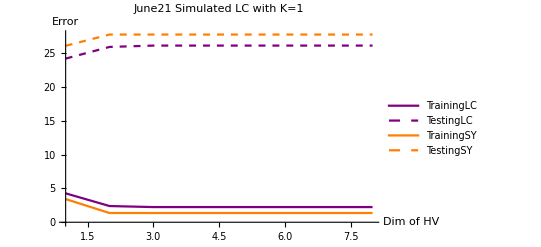

```mathematica
DiscretePlot[{m2LCk1LCTR[[k]],m2LCk1LCTE[[k]],m2LCk1SYTR[[k]],m2LCk1SYTE[[k]]},{k,1,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated LC with K=1",AxesLabel->{"Dim of HV","Error"}]
```

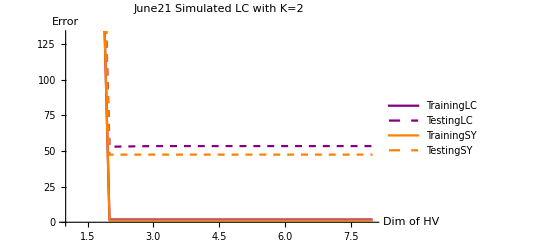

```mathematica
DiscretePlot[{m2LCk2LCTR[[k]],m2LCk2LCTE[[k]],m2LCk2SYTR[[k]],m2LCk2SYTE[[k]]},{k,1,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated LC with K=2",AxesLabel->{"Dim of HV","Error"}]
```

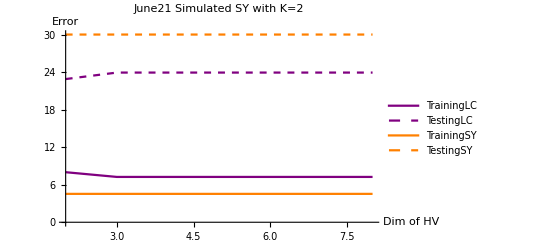

```mathematica
DiscretePlot[{m2SYk2LCTR[[k]],m2SYk2LCTE[[k]],m2SYk2SYTR[[k]],m2SYk2SYTE[[k]]},{k,2,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated SY with K=2",AxesLabel->{"Dim of HV","Error"}]
```

```mathematica
DiscretePlot[{LCk3LCTR[[k]],LCk3LCTE[[k]],LCk3SYTR[[k]],LCk3SYTE[[k]]},{k,2,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated LC with K=3",AxesLabel->{"Dim of HV","Error"}]
```

Part::partd: Part specification LCk3LCTR⟦2⟧ is longer than depth of object.

Part::partd: Part specification LCk3LCTR⟦3⟧ is longer than depth of object.

Part::partd: Part specification LCk3LCTR⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

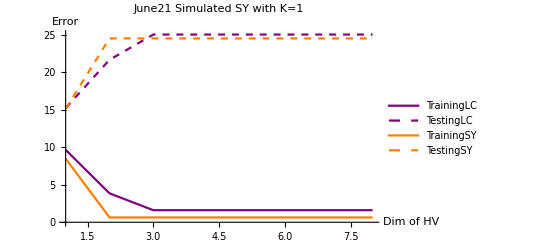

```mathematica
DiscretePlot[{SYk1LCTR[[k]],SYk1LCTE[[k]],SYk1SYTR[[k]],SYk1SYTE[[k]]},{k,1,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated SY with K=1",AxesLabel->{"Dim of HV","Error"}]
```

```mathematica
DiscretePlot[{LCk4LCTR[[k]],LCk4LCTE[[k]],LCk4SYTR[[k]],LCk4SYTE[[k]]},{k,2,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June21 Simulated LC with K=4",AxesLabel->{"Dim of HV","Error"}]
```

Part::partd: Part specification LCk4LCTR⟦2⟧ is longer than depth of object.

Part::partd: Part specification LCk4LCTR⟦3⟧ is longer than depth of object.

Part::partd: Part specification LCk4LCTR⟦4⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

## CurrentDATA for 6meas

m6LC1kSYTR means this is for 6 measurements, the simulated data is from a local causal model with K=1 and the fit was done using an SY causal model and this is the training errors. 

For 6 measurements I have been using 8 different random seeds of the minimization Nelder-Mead method when doing local causal fits and 10 seeds for SY causal fits. This is to deal with the local minimum problem which begins to arise when fitting experiments with more measurements despite the fact that Nelder-Mead is a global minimum technique.

```mathematica
m6LC1kLCTR = {149.77313930272172,136.59876082190374,127.53363844110518,122.49112217782334,118.99088548727954,117.84817873559983,117.73096353112736,117.73096351118436,117.73096351566863,117.7};
m6LC1kLCTE = {227.7708202635526,255.41541374301093,258.0994529972481,267.81300001613226,273.2728687036431,274.11915827282,272.9441087572567,272.9443074574259,272.9441856993059,272.9443714242111};
m6LC1kSYTR = {98.39323363960017,69.63923639663213,69.63923634732949,69.6392363479601,69.639};
m6LC1kSYTE = {352.2653964185366,389.9584927985865,389.95792301587164,389.95770401057916,389.95808129418367};
m6LC2kLCTR = {20656.592756512528,173.0518466842014,148.08761355665274,140.34846562454828,135.58617627181937};
m6LC2kLCTE = {21654.07917764522,298.47460050474183,326.1792029564929,335.2161564142041,334.0972529866354};
m6LC2kSYTR = {18044.08998239193,92.52759389121871,92.52759389102033,92.52759389060422,92.52759389068343};
m6LC2kSYTE = {19137.475160316895,373.0982486465905,373.09831592653904,373.09822344899794,373.0981874849086};
m6SY2kLCTR ={382393.2643094346,372874.72399717104,365838.9429097206,363079.8974222648,361837.51803985855,361359.15506990434};
m6SY2kLCTE = {396252.3939869049,386776.10201794596,378838.4588388897,376665.5241427901,375485.74055752624,375218.4119995291};
m6SY2kSYTR ={5006.412983836558,36.57784017711522,36.57784016938128,36.57784016930434,36.57784016890844,36.577840168963206};
m6SY2kSYTE = {5000.210484676294,269.6907568623905,269.69101589562297,269.69099055966785,269.69095236676134,269.6909724738655};
m6SYQTR = 364189;
m6SYQTE = 377197.7577087963;
(*m6LC3kLCTR = ;
m6LC3kLCTE = ;
m6LC3kSYTR = ;
m6LC3kSYTE = ;*)
m6EntLCTR = {1.4237687768758489*^6,492579.1583744512,201905.63228736768,89862.80294348557,57011.49175249981,62644.466616014244,39766.71586106525,39284.634166127325};
m6EntLCTE = {1.4289535414808164*^6,492680.9480170601,201458.512125506,91590.96090275468,57448.7538074402,63404.89326857554,40308.063313937775,39884.974457461765};
m6EntSYTR = {1.1518909216306515*^6,24089.268033112276,74.97281400445601,74.97228774512894,74.97228775793995,74.97228774150902,74.9722877740537,74.97228813680067};
m6EntSYTE = {1.1619930375035866*^6,24462.101923742746,480.00004452247873,479.9627839312426,479.9641374327226,479.9625671338323,479.9645717534688,479.95925974351474};
m6EntQTR = ConstantArray[143.34334630653166,8];
m6EntQTE = ConstantArray[398.7985624055574,8];
```

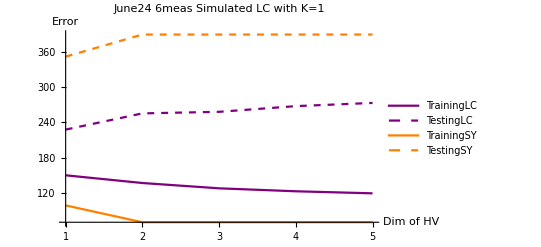

```mathematica
DiscretePlot[{m6LC1kLCTR[[k]],m6LC1kLCTE[[k]],m6LC1kSYTR[[k]],m6LC1kSYTE[[k]]},{k,1,5},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June24 6meas Simulated LC with K=1",AxesLabel->{"Dim of HV","Error"}]
```

```mathematica
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

{0,0,0,0,0,62644.5,39766.7,39284.6}

{0,0,0,0,0,63404.9,40308.1,39885.}

{0,0,0,0,0,74.9723,74.9723,74.9723}

{0,0,0,0,0,479.963,479.965,479.959}

```mathematica
{0,0,0,0,0,74.97228774150902,74.9722877740537,74.97228813680067`74.97228774150902`,74.9722877740537,74.97228813680067`7}
```

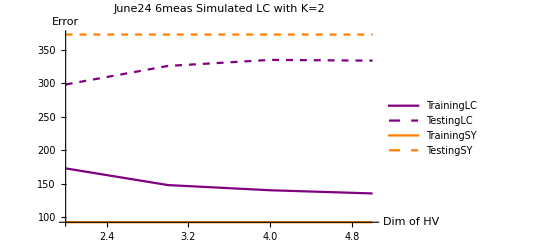

```mathematica
DiscretePlot[{m6LC2kLCTR[[k]],m6LC2kLCTE[[k]],m6LC2kSYTR[[k]],m6LC2kSYTE[[k]]},{k,2,5},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June24 6meas Simulated LC with K=2",AxesLabel->{"Dim of HV","Error"}]
```

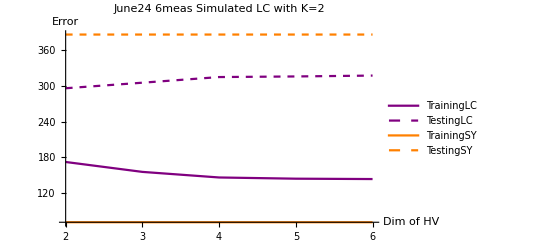

```mathematica
DiscretePlot[{m6SY2kLCTR[[k]],m6SY2kLCTE[[k]],m6SY2kSYTR[[k]],m6SY2kSYTE[[k]]},{k,2,6},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June24 6meas Simulated LC with K=2",AxesLabel->{"Dim of HV","Error"}]
```

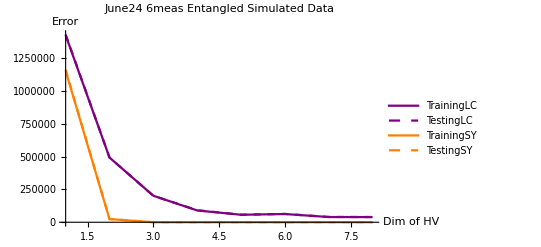

```mathematica
DiscretePlot[{m6EntLCTR[[k]],m6EntLCTE[[k]],m6EntSYTR[[k]],m6EntSYTE[[k]]},{k,1,8},PlotLegends -> {"TrainingLC","TestingLC","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Orange},{Dashed,Orange}},PlotLabel->"June24 6meas Entangled Simulated Data",AxesLabel->{"Dim of HV","Error"}]
```

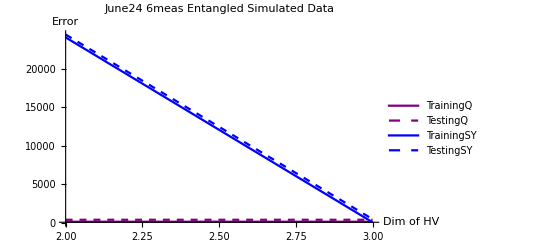

```mathematica
DiscretePlot[{m6EntQTR[[k]],m6EntQTE[[k]],m6EntSYTR[[k]],m6EntSYTE[[k]]},{k,2,3},PlotLegends -> {"TrainingQ","TestingQ","TrainingSY","TestingSY"},Filling->None,Joined->True,PlotStyle->{{Thick,Purple},{Dashed,Purple},{Thick,Blue},{Dashed,Blue}},PlotLabel->"June24 6meas Entangled Simulated Data",AxesLabel->{"Dim of HV","Error"},PlotRange->All]
```

```mathematica
{0,0,1}
```

```mathematica
713.9126196880736
```

```mathematica
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

{493242.,187543.,103995.,50705.3,38686.4,32901.6,31863.2,24609.8}

{463169.,182988.,99879.,49805.1,37900.8,32547.2,31439.8,24169.6}

{430889.,271.02,192.768,192.768,0,0,0,0}

{408813.,1582.79,1363.32,1363.32,0,0,0,0}

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

155.54

316.718

{0,0,24306.5}

{0,0,24143.5}

{0,0,64.2677}

{0,0,405.845}

```mathematica
M
```

6

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

155.54

316.718

{0,0,24306.5}

{0,0,24143.5}

{0,0,64.2677}

{0,0,405.845}

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

155.54

316.718

{0,0,24306.5}

{0,0,24143.5}

{0,0,64.2677}

{0,0,405.845}

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

155.54

316.718

{258355.,45947.4,24306.5,9767.28}

{263415.,45020.8,24143.5,10099.}

{204145.,64.2677}

{206897.,405.845}

```mathematica
TrainingLossQ
TestingLossQ
TrainingLossLC
TestingLossLC
TrainingLossSY
TestingLossSY
```

296.799

585.77

{2.41535×10^6,416054.,234109.,84572.6,67461.6,56051.3,46473.4,53556.9}

{2.40667×10^6,419440.,231989.,86225.1,69351.2,56239.1,47503.,54602.2}

{1.94236×10^6,114.001,114.001,0}

{1.95627×10^6,887.004,887.004,0}

```mathematica
test = {1,2,3}
```

{1,2,3}

```mathematica
Log[2*π*test]
```

{Log[2 π],Log[4 π],Log[6 π]}

Resampling...

Completed B= 1

Completed B= 2

Completed B= 3

Completed B= 4

Completed B= 5

0.001504430.2534870.002065960.252137

## Finding amount of signalling in a fit

```mathematica
Clear[a,b,c];
K=2;M=6;
X0vec = Array[a,K*M];
Y0vec = Array[b,K*M*M];
X1vec=ConstantArray[1,Dimensions[X0vec]]-X0vec;
Y1vec=ConstantArray[1,Dimensions[Y0vec]]-Y0vec;
Λvectemp = Array[c,K];
Λvec = Λvectemp/Total[Λvectemp];
Parameters = ArrayReshape[{X0vec,Y0vec,Λvectemp},Length[X0vec]+Length[Y0vec]+Length[Λvectemp]];
X0 = ArrayReshape[X0vec,{M,K}];
X1 = ArrayReshape[X1vec,{M,K}];  (*s,lambda*)
Y0 = ArrayReshape[Y0vec,{K,M,M}]; (*lambda,s,t*)
Y1 = ArrayReshape[Y1vec,{K,M,M}];
Λ = DiagonalMatrix[Λvec];
U00 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U00[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U01 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U01[[s,t]] = Sum[Λvec[[k]]*X0 [[s,k]]*Y1[[k,s,t]],{k,1,K}]]];
U10 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U10[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y0 [[k,s,t]],{k,1,K}]]];
U11 = ConstantArray[0,{M,M}] ;
For[s=1,s≤M,s++,For[t=1,t≤M,t++,U11[[s,t]] = Sum[Λvec[[k]]*X1 [[s,k]]*Y1 [[k,s,t]],{k,1,K}]]];
U00vec=ArrayReshape[U00,M*M];
U01vec=ArrayReshape[U01,M*M];
U10vec=ArrayReshape[U10,M*M];
U11vec=ArrayReshape[U11,M*M];
Uvec = ConstantArray[0,{M*M,4}];
Uvec[[;;,1]] = U00vec;
Uvec[[;;,2]] = U01vec;
Uvec[[;;,3]] = U10vec;
Uvec[[;;,4]] = U11vec;
```

```mathematica
U00vec
```

{(a[1] b[1] c[1])/(c[1]+c[2])+(a[2] b[37] c[2])/(c[1]+c[2]),(a[1] b[2] c[1])/(c[1]+c[2])+(a[2] b[38] c[2])/(c[1]+c[2]),(a[1] b[3] c[1])/(c[1]+c[2])+(a[2] b[39] c[2])/(c[1]+c[2]),(a[1] b[4] c[1])/(c[1]+c[2])+(a[2] b[40] c[2])/(c[1]+c[2]),(a[1] b[5] c[1])/(c[1]+c[2])+(a[2] b[41] c[2])/(c[1]+c[2]),(a[1] b[6] c[1])/(c[1]+c[2])+(a[2] b[42] c[2])/(c[1]+c[2]),(a[3] b[7] c[1])/(c[1]+c[2])+(a[4] b[43] c[2])/(c[1]+c[2]),(a[3] b[8] c[1])/(c[1]+c[2])+(a[4] b[44] c[2])/(c[1]+c[2]),(a[3] b[9] c[1])/(c[1]+c[2])+(a[4] b[45] c[2])/(c[1]+c[2]),(a[3] b[10] c[1])/(c[1]+c[2])+(a[4] b[46] c[2])/(c[1]+c[2]),(a[3] b[11] c[1])/(c[1]+c[2])+(a[4] b[47] c[2])/(c[1]+c[2]),(a[3] b[12] c[1])/(c[1]+c[2])+(a[4] b[48] c[2])/(c[1]+c[2]),(a[5] b[13] c[1])/(c[1]+c[2])+(a[6] b[49] c[2])/(c[1]+c[2]),(a[5] b[14] c[1])/(c[1]+c[2])+(a[6] b[50] c[2])/(c[1]+c[2]),(a[5] b[15] c[1])/(c[1]+c[2])+(a[6] b[51] c[2])/(c[1]+c[2]),(a[5] b[16] c[1])/(c[1]+c[2])+(a[6] b[52] c[2])/(c[1]+c[2]),(a[5] b[17] c[1])/(c[1]+c[2])+(a[6] b[53] c[2])/(c[1]+c[2]),(a[5] b[18] c[1])/(c[1]+c[2])+(a[6] b[54] c[2])/(c[1]+c[2]),(a[7] b[19] c[1])/(c[1]+c[2])+(a[8] b[55] c[2])/(c[1]+c[2]),(a[7] b[20] c[1])/(c[1]+c[2])+(a[8] b[56] c[2])/(c[1]+c[2]),(a[7] b[21] c[1])/(c[1]+c[2])+(a[8] b[57] c[2])/(c[1]+c[2]),(a[7] b[22] c[1])/(c[1]+c[2])+(a[8] b[58] c[2])/(c[1]+c[2]),(a[7] b[23] c[1])/(c[1]+c[2])+(a[8] b[59] c[2])/(c[1]+c[2]),(a[7] b[24] c[1])/(c[1]+c[2])+(a[8] b[60] c[2])/(c[1]+c[2]),(a[9] b[25] c[1])/(c[1]+c[2])+(a[10] b[61] c[2])/(c[1]+c[2]),(a[9] b[26] c[1])/(c[1]+c[2])+(a[10] b[62] c[2])/(c[1]+c[2]),(a[9] b[27] c[1])/(c[1]+c[2])+(a[10] b[63] c[2])/(c[1]+c[2]),(a[9] b[28] c[1])/(c[1]+c[2])+(a[10] b[64] c[2])/(c[1]+c[2]),(a[9] b[29] c[1])/(c[1]+c[2])+(a[10] b[65] c[2])/(c[1]+c[2]),(a[9] b[30] c[1])/(c[1]+c[2])+(a[10] b[66] c[2])/(c[1]+c[2]),(a[11] b[31] c[1])/(c[1]+c[2])+(a[12] b[67] c[2])/(c[1]+c[2]),(a[11] b[32] c[1])/(c[1]+c[2])+(a[12] b[68] c[2])/(c[1]+c[2]),(a[11] b[33] c[1])/(c[1]+c[2])+(a[12] b[69] c[2])/(c[1]+c[2]),(a[11] b[34] c[1])/(c[1]+c[2])+(a[12] b[70] c[2])/(c[1]+c[2]),(a[11] b[35] c[1])/(c[1]+c[2])+(a[12] b[71] c[2])/(c[1]+c[2]),(a[11] b[36] c[1])/(c[1]+c[2])+(a[12] b[72] c[2])/(c[1]+c[2])}